# Virulence-Tolerance Evolution in metapopulations

## Ecological model & Trade-offs

## Within-Host model

Let X be the density of pathogen

```mathematica
dX = (β0 θ-β1 X)X -μ X - d X - γ0 σ X
```

-d X+X (-X β1+β0 θ)-X μ-X γ0 σ

β0 is growth and β1 the strength of density dependance on growth.
μ is the ‘natural’ mortality rate
d the dispersal rate
γ0 the  maximal Host-induced mortality rate
σ the investment in resistance

```mathematica
Localeq = FullSimplify[Solve[dX ==0, X]]
```

{{X→0},{X→-(d-β0 θ+μ+γ0 σ)/β1}}

```mathematica
Xeq[σ_, θ_]:=-(d-β0 θ+μ+γ0 σ)/β1
```

It is easy to determine that Infected host can clear heir parasites trough immune investment when γ = β0-d-μ

## Between-Host Model

We assume that Within-host dynamics occurs at a faster time scale than between host dynamics, such that we reach within-host equilibrium before any transmission event.
We thus track the frequency of patches that are Unavailable, Disease-free, or Infected.

```mathematica
dPS = b0  (1-pS-pI) pS+bi[σ] (1-pS-pI) pI - d0 pS - β[σ, θ] pI pS + τ[σ, θ] pI
dPI = β[σ, θ] pI pS - d0 pI - α[σ, θ] pI - τ[σ, θ] pI
```

-d0 pS+b0 (1-pI-pS) pS+pI (1-pI-pS) bi[σ]-pI pS β[σ,θ]+pI τ[σ,θ]

-d0 pI-pI α[σ,θ]+pI pS β[σ,θ]-pI τ[σ,θ]

```mathematica
MetaEq = Solve[{dPS==0, dPI==0},{pS, pI}]// FullSimplify
```

{{pS→0,pI→0},{pS→1-d0/b0,pI→0},{pS→(d0+α[σ,θ]+τ[σ,θ])/β[σ,θ],pI→-1/(2 bi[σ] β[σ,θ]^2)((d0-bi[σ]+α[σ,θ]) β[σ,θ]^2+(b0+bi[σ]) β[σ,θ] (d0+α[σ,θ]+τ[σ,θ])+√(β[σ,θ]^2 (-4 bi[σ] (d0+α[σ,θ]+τ[σ,θ]) (b0 α[σ,θ]+(-b0+d0) β[σ,θ]+b0 (d0+τ[σ,θ]))+((d0+α[σ,θ]) (b0+β[σ,θ])+b0 τ[σ,θ]+bi[σ] (d0+α[σ,θ]-β[σ,θ]+τ[σ,θ]))^2)))},{pS→(d0+α[σ,θ]+τ[σ,θ])/β[σ,θ],pI→1/(2 bi[σ] β[σ,θ]^2)(-((d0-bi[σ]+α[σ,θ]) β[σ,θ]^2)-(b0+bi[σ]) β[σ,θ] (d0+α[σ,θ]+τ[σ,θ])+√(β[σ,θ]^2 (-4 bi[σ] (d0+α[σ,θ]+τ[σ,θ]) (b0 α[σ,θ]+(-b0+d0) β[σ,θ]+b0 (d0+τ[σ,θ]))+((d0+α[σ,θ]) (b0+β[σ,θ])+b0 τ[σ,θ]+bi[σ] (d0+α[σ,θ]-β[σ,θ]+τ[σ,θ]))^2)))}}

```mathematica
pS[σ_, θ_]:=(d0+α[σ,θ]+τ[σ,θ])/β[σ,θ];
pI[σ_, θ_]:=1/(2 bi[σ] β[σ,θ]^2)(-((d0-bi[σ]+α[σ,θ]) β[σ,θ]^2)-(b0+bi[σ]) β[σ,θ] (d0+α[σ,θ]+τ[σ,θ])+√(β[σ,θ]^2 (-4 bi[σ] (d0+α[σ,θ]+τ[σ,θ]) (b0 α[σ,θ]+(-b0+d0) β[σ,θ]+b0 (d0+τ[σ,θ]))+((d0+α[σ,θ]) (b0+β[σ,θ])+b0 τ[σ,θ]+bi[σ] (d0+α[σ,θ]-β[σ,θ]+τ[σ,θ]))^2)));
pI2version[σ_, θ_]:=-1/(2 bi[σ] β[σ,θ]^2)((d0-bi[σ]+α[σ,θ]) β[σ,θ]^2+(b0+bi[σ]) β[σ,θ] (d0+α[σ,θ]+τ[σ,θ])+√(β[σ,θ]^2 (-4 bi[σ] (d0+α[σ,θ]+τ[σ,θ]) (b0 α[σ,θ]+(-b0+d0) β[σ,θ]+b0 (d0+τ[σ,θ]))+((d0+α[σ,θ]) (b0+β[σ,θ])+b0 τ[σ,θ]+bi[σ] (d0+α[σ,θ]-β[σ,θ]+τ[σ,θ]))^2)));
p0[σ_, θ_]:= 1-pS[σ, θ]-pI[σ, θ]
Psdfe = 1-d0/b0
```

1-d0/b0

## Trade-offs & Epidemiological Functions

### Fecundity-Resistance Trade-off

```mathematica
bi[σ_]:=  b0 (1-σ/(ϵ -(ϵ-1)σ));
```

```mathematica
plot1=Plot[bi[σ]/.{ b0->4,ϵ->5}, {σ, 0,1},PlotRange->All,Frame->True,FrameLabel->{"σ"," b(σ)"},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},PlotLabels->Placed["ϵ=5", {0.5,0.8}],ImageSize->360];
plot2=Plot[bi[σ]/.{ b0->4, ϵ->1}, {σ, 0,1},PlotRange->All,Frame->True,FrameLabel->{"σ"," b(σ)"},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},PlotLabels->Placed["ϵ=1", {0.4,0.5}],ImageSize->360];
plot3=Plot[bi[σ]/.{b0->4, ϵ->0.1}, {σ, 0,1},PlotRange->All,Frame->True,FrameLabel->{"σ"," b(σ)"},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},PlotLabels->Placed["ϵ=0.1", {0.2,0.2}],ImageSize->360];
```

```mathematica
MyFinalPlot = Rasterize[Show[plot1,plot2, plot3]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Julien\\Desktop\\Figures Finales Evol-VirRes\\Tradeoffplot.png",MyFinalPlot,Background->None]
```

C:\Users\Julien\Desktop\Figures Finales Evol-VirRes\Tradeoffplot.png

### Density-Mortality Trade-off

```mathematica
α[σ_, θ_]:=α0 (Xeq[σ, θ]/Xeq[0, 1])/ (ϵv-(ϵv-1)(Xeq[σ, θ]/Xeq[0, 1]))
```

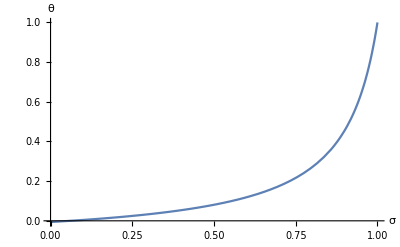

```mathematica
Plot[α[σ, θ]/. {α0->1,τ->0.1,ϵr->1,b0-> 3, d->0.5, μ->0.1, γ0->1, β0->10,β1->0.01,  ϵv->10, σ->0}, {θ,0,1}, PlotRange->All, AxesLabel->{"σ", "θ"}]
```

We must always have d+μ+γ0 (ϵv+σ-ϵv σ)-β0[θ] =/= 0

### Recovery-Density trade-off

```mathematica
τ[σ_, θ_]:= τ0 (1-(Xeq[σ, θ]/Xeq[0, 1]))/ (ϵr-(ϵr-1)(1-(Xeq[σ, θ]/Xeq[0, 1])))
```

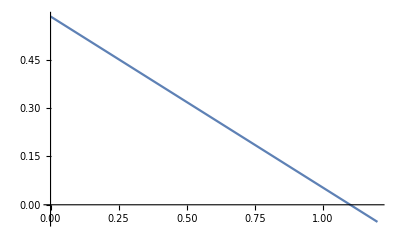

```mathematica
Plot[τ[σ,θ]/.{τ0->0.5, d->0.5, μ->0.1, γ0->1, β0->10, β1->0.04, α->1, ϵr->1, σ->1}, {θ, 0,1.2}, PlotRange->All]
```

### Transmission function

```mathematica
β[σ_, θ_]:= d(1-ρ) Xeq[σ, θ]
```

## Host Evolution

## Invasion Fitness

### Invasion fitness

The jacobian matrix of the mutant

```mathematica
JacMut[σ_, σmut_]:=({{b0  p0[σ]-β[σ, θ] pI[σ]-d0, bi[σmut] p0[σ]+τ[σmut, θ]}, {β[σ, θ] pI[σ], -d0-τ r[σmut]-α[σmut, θ]}})
```

```mathematica
(*Eigenvalues[JacMutOLD[σ, σmut]]// FullSimplify
```

Decomposing the jacobian for the use of next generation theorem

```mathematica
F[σ_, σmut_]:= ({{b0  p0[σ], bi[σmut] p0[σ]}, {0, 0}})
```

```mathematica
V[σ_, σmut_]:= ({{d0+β[σ] pI[σ], -τ[σmut]}, {-β[σ] pI[σ], ψ[σmut]}})
```

```mathematica
NGM[σ_, σmut_]:=F[σ, σmut]. Inverse[V[σ, σmut]]
```

```mathematica
Eigenvalues[NGM[σ, σmut]]// FullSimplify
```

{0,(p0[σ] (b[σmut] pI[σ] β[σ]+b0 ψ[σmut]))/(d0 ψ[σmut]+pI[σ] β[σ] (-τ[σmut]+ψ[σmut]))}

```mathematica
NGTFitnessFunction[σ_,σmut_]:=(b0 p0[σ,θ] (d0+τ[σmut,θ]+α[σmut,θ])- bi[σmut]p0[σ,θ]d (-1+ρ)  pI[σ,θ] Xeq[σ,θ])/(d0 τ[σmut,θ]+(d0+α[σmut,θ]) (d0-d (-1+ρ) pI[σ,θ] Xeq[σ,θ]))
```

Quick Check for neutrality

```mathematica
ESSparameters =  {ϵ->3, b0->1, μ->0.5, α0->0.5, β0->3,θ->1, β1->0.04,  ρ ->0.9 ,γ0->1.5, d0->0.05, τ0->0.1, ϵv->0.8, ϵr->1, d->0.2}
```

{ϵ→3,b0→1,μ→0.5,α0→0.5,β0→3,θ→1,β1→0.04,ρ→0.9,γ0→1.5,d0→0.05,τ0→0.1,ϵv→0.8,ϵr→1,d→0.2}

```mathematica
NGTFitnessFunction[0.5,0.5]//. ESSparameters
```

1.

R0 definition

```mathematica
R0[σ_, θ_]:= d (1-ρ) Xeq[σ, θ] / ( d0+ α v[σ, θ]+ τ r[σ, θ])
```

PIP

```mathematica
ESSparameters = { b0->0.8, μ->0.5, α0->1, β0->10,θ->0.8, β1->0.04,  ρ ->0.9 ,γ0->1, d0->0.05, τ0->1, ϵv->3, ϵr->1,  d->0.5, ϵ->0.2}
```

{b0→0.8,μ→0.5,α0→1,β0→10,θ→0.8,β1→0.04,ρ→0.9,γ0→1,d0→0.05,τ0→1,ϵv→3,ϵr→1,d→0.5,ϵ→0.2}

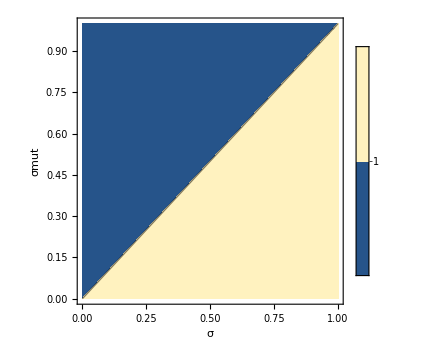

```mathematica
MyContourPlot = ContourPlot[Evaluate[NGTFitnessFunction[σ,σmut ]] /.ESSparameters ,{σ,0,1},{σmut,0,1},PlotRange->All, Contours->{1} ,FrameLabel->{σ, σmut} , PlotLegends->Automatic, PlotPoints->25 ,Frame->True,FrameLabel->{Style["Dispersal rate", Bold, 10],Style[ "ESS Resistance", Bold, 10]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, Background->White]
```

```mathematica
Export["C:\\Users\\Julien\\Desktop\\Figures virulence tolerance MAJ Juin 2024\\ Host evolution REP.png", MyContourPlot, Background-> None]
```

C:\Users\Julien\Desktop\Figures virulence tolerance MAJ Juin 2024\ Host evolution REP.png

## Singular strategies

### Derivatives of the fitness function

The fitness Gradient

```mathematica
MarginalFitness[σESS_]:= D[NGTFitnessFunction[σ,σmut],σmut]//. {σ-> σESS, σmut -> σESS};
```

The two second derivatives

```mathematica
ESSStab[σ_,σmut_]:= D[D[NGTFitnessFunction[σ,σmut],σmut],σmut]
```

```mathematica
d2Wdσmut2[σESS_]:= ESSStab[σ,σmut]//. {σ-> σESS, σmut -> σESS}
```

```mathematica
ConvergenceStab[σ_,σmut_]:= D[D[NGTFitnessFunction[σ,σmut],σ],σ]
```

```mathematica
d2Wdσ2[σESS_]:= ConvergenceStab[σ,σmut]//. {σ-> σESS, σmut -> σESS}
```

### Viable ESS and the trade-off forms

#### Fecundity Trade-off form

Previous parameters for figures

```mathematica
ESSparameters = { b0->0.8, μ->0.5, α0->1, β0->10,θ->0.8, β1->0.04,  ρ ->0.9 ,γ0->1, d0->0.05, τ0->1, ϵv->3, ϵr->1,  d->0.5}
```

{b0→0.8,μ→0.5,α0→1,β0→10,θ→0.8,β1→0.04,ρ→0.9,γ0→1,d0→0.05,τ0→1,ϵv→3,ϵr→1,d→0.5}

```mathematica
Nresults = {}
Do[
(* For each steps, we follow this procedure*)
(* a. Get singular strategies by numerically solving fitness gradient = 0 *)
Print[dd];

NumESS= Evaluate[MarginalFitness[σESS]/.ESSparameters /. ϵ-> dd]; (*Evaluate fitness for current param value *)

NumSolESS = NSolve[Evaluate[NumESS] ==0 &&0<σESS<1,σESS,Reals];(* Get singular values that are real & between ]0,1[ *)
Listsingular = N[NumSolESS];

ListCandidates = σESS /. Listsingular;


(* For the remaining candidates, we determine if they are in the viability domain of α -> R0 > 1 & RM > 1*)
ViableCandidates = {};

Do[
Testedθ = θ /. ESSparameters;
Testedσ =ListCandidates[[i]];
PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. ϵ-> dd];

(* OK*)
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. ϵ-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //. ϵ-> dd];

If[(PS>0 && PI >=0 && X>=0),AppendTo[ViableCandidates,ListCandidates[[i]]]] ; 
,{i,1,Length[ListCandidates]}];
Print[ViableCandidates];

(* b. NON-Invadability : Get the second derivative with respect to αmut and keep αESS values for which it's negative *)

NumDerivativeESS= Evaluate[d2Wdσmut2[σESS]/.ESSparameters /. ϵ-> dd];
ESSStableCandidates = {};
Do[
ESSstableValue = Evaluate[NumDerivativeESS/. σESS ->ViableCandidates[[i]]];
AppendTo[ESSStableCandidates,{ViableCandidates[[i]],ESSstableValue}];
,{i,1,Length[ViableCandidates]}];
(* Here we get non invadable values *)
AdmissiblesCandidates =Cases[ESSStableCandidates, s_/;AnyTrue[s, Negative]];
(*Print[AdmissiblesCandidates];*)
(* Check convergence stability : Get the second derivative with respect to αres at αESS, and keep the positive ones *)
Admissibleα = {};
AdmissibleDerivative = {};
Do[
σValue = AdmissiblesCandidates[[i,1]];
DValue = AdmissiblesCandidates[[i,2]];
AppendTo[Admissibleα,σValue];
AppendTo[AdmissibleDerivative,DValue]
,{i,1,Length[AdmissiblesCandidates]}];
(*Print[Admissibleα];*)

NumDerivativeCONV= Evaluate[d2Wdσ2[σESS]]/.ESSparameters/. ϵ-> dd;
Conv = {};
Do[
ESSstableValue = Evaluate[NumDerivativeCONV/. σESS ->Admissibleα[[i]]];
AppendTo[Conv,{Admissibleα[[i]],AdmissibleDerivative[[i]],ESSstableValue}];
,{i,1,Length[Admissibleα]}];

ESSvalues= {};
Do[
If[Conv[[i]][[3]] > Conv[[i]][[2]],AppendTo[ESSvalues,Conv[[i]][[1]]]] ; (* 3. Second derivative to α / 2. Second derivative to αmut /
 1.αvalue*)
,{i,1,Length[Conv]}];

AppendTo[Nresults,{dd,ESSvalues}];
,{dd,0.3,6,1/10}]

Print[Nresults];
```

{}

0.3

{}

0.4

{}

0.5

{}

0.6

{}

0.7

{}

0.8

{}

0.9

{}

1.

{}

1.1

{}

1.2

{}

1.3

{}

1.4

{}

1.5

{}

1.6

{}

1.7

{}

1.8

{}

1.9

{}

2.

{}

2.1

{}

2.2

{}

2.3

{}

2.4

{}

2.5

{}

2.6

{}

2.7

{}

2.8

{}

2.9

{}

3.

{}

3.1

{0.00620911}

3.2

{0.0255126}

3.3

{0.043659}

3.4

{0.0607608}

3.5

{0.0769159}

3.6

{0.0922096}

3.7

{0.106717}

3.8

{0.120505}

3.9

{0.133631}

4.

{0.146147}

4.1

{0.158101}

4.2

{0.169534}

4.3

{0.180483}

4.4

{0.190982}

4.5

{0.201062}

4.6

{0.21075}

4.7

{0.220071}

4.8

{0.22905}

4.9

{0.237706}

5.

{0.246058}

5.1

{0.254125}

5.2

{0.261923}

5.3

{0.269466}

5.4

{0.276769}

5.5

{0.283844}

5.6

{0.290703}

5.7

{0.297357}

5.8

{0.303816}

5.9

{0.31009}

6.

{0.316188}

{{0.3,{}},{0.4,{}},{0.5,{}},{0.6,{}},{0.7,{}},{0.8,{}},{0.9,{}},{1.,{}},{1.1,{}},{1.2,{}},{1.3,{}},{1.4,{}},{1.5,{}},{1.6,{}},{1.7,{}},{1.8,{}},{1.9,{}},{2.,{}},{2.1,{}},{2.2,{}},{2.3,{}},{2.4,{}},{2.5,{}},{2.6,{}},{2.7,{}},{2.8,{}},{2.9,{}},{3.,{}},{3.1,{0.00620911}},{3.2,{0.0255126}},{3.3,{0.043659}},{3.4,{0.0607608}},{3.5,{0.0769159}},{3.6,{0.0922096}},{3.7,{0.106717}},{3.8,{0.120505}},{3.9,{0.133631}},{4.,{0.146147}},{4.1,{0.158101}},{4.2,{0.169534}},{4.3,{0.180483}},{4.4,{0.190982}},{4.5,{0.201062}},{4.6,{0.21075}},{4.7,{0.220071}},{4.8,{0.22905}},{4.9,{0.237706}},{5.,{0.246058}},{5.1,{0.254125}},{5.2,{0.261923}},{5.3,{0.269466}},{5.4,{0.276769}},{5.5,{0.283844}},{5.6,{0.290703}},{5.7,{0.297357}},{5.8,{0.303816}},{5.9,{0.31009}},{6.,{0.316188}}}

```mathematica
ListValuesϵ = {}

Do[
AppendTo[ListValuesϵ, {Nresults[[i]][[1]],Nresults[[i]][[2]][[1]]}];
,{i,1,Length[Nresults]}]
```

{}

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
plotset = {PlotStyle-> Thick, Background-> None, AxesStyle-> Thick, FrameStyle-> Thick, LabelStyle-> Thick};
```

```mathematica
mycolor=Function[{x,y},If[31/1000<x<= 101/1000,Red,Blue]];
plot =Rasterize[ListPlot[ListValuesϵ, ColorFunction->mycolor,ColorFunctionScaling->False, AxesLabel->{"ϵ,""ESS resistance"},PlotRange->All,Frame->True,FrameLabel->{Style["ϵ", Bold, 14],Style[ "ESS resistance", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, Joined->True]]
```

-Graphics-

```mathematica
Export["C:\\Users\\Julien\\Desktop\\Figures virulence tolerance MAJ Juin 2024\\ Host ESS versus trade off.png",plot ,Background->None]
```

C:\Users\Julien\Desktop\Figures virulence tolerance MAJ Juin 2024\ Host ESS versus trade off.png

## Parasite Evolution

## Pre-requisite : Competition dynamics in coinfected hosts

### Competition Dynamics in a shared patch

Dynamics of a shared patch with f the frequency of strain 1 and (1-f) the frequency of strain 2
The equilibrium depends on f, which in turn changes trough time

```mathematica
dXt = β0 θ X(1-f)+ β0 θmut X f -β1 X^2 -μ X - d X - γ0 σ X
```

-d X-X^2 β1+(1-f) X β0 θ+f X β0 θmut-X μ-X γ0 σ

```mathematica
Eqtwin = FullSimplify[Solve[dXt==0, X]]
```

{{X→0},{X→-(d+(-1+f) β0 θ-f β0 θmut+μ+γ0 σ)/β1}}

```mathematica
Y[σ_,θ_, θmut_]:=  Evaluate[X /. Eqtwin [[2]] ]
```

f describe the frequency of mutant Xm in a shared patch.
By hand, pen & paper, we determine that the dynamics of frequency is given by

```mathematica
df= ( β0 θmut -β0 θ ) f(1-f)
```

(1-f) f (-β0 θ+β0 θmut)

```mathematica
delta[θ_,θmut_] := ( β0 θmut -β0 θ )
(* We derive intial conditions of interest, following a given reinvasion*)
ϕrm[θ_] :=1/(Xeq[σ, θ]+1) (* Imut is obtained in the first subsection *)
ϕmr[θ_]:=Xeq[σ, θ]/(Xeq[σ, θ]+1)
```

Define Function describing the change in frequency according to two invasion scenarios (Mut by Res VS Res by Mut)

```mathematica
frm[θ_, θmut_,t_]:= ϕrm[θ] / (ϕrm[θ] +(1-ϕrm[θ])Exp[-delta[θ, θmut]  t])
fmr[θ_, θmut_,t_]:= ϕmr[θmut] / (ϕmr[θmut] +(1-ϕmr[θmut])Exp[-delta[θ, θmut]  t])
```

```mathematica
Ieqm[σ_,θ_, θmut_,t_] :=Y[σ,θ, θmut] /. f->frm[θ,θmut,t]
Ieqr[σ_,θ_, θmut_,t_] := Y[σ,θ, θmut] /. f->fmr[θ, θmut,t]
```

Integral Function describing the change in frequency trough time until extinction !

We redefine function v and r to account for the quasi-equilibrium (using an approximation by taylor expanding the function at first order)

```mathematica
Series[α[θmut, θ, t], {θmut, θ, 1}]
Series[α[θ, θmut, t], {θmut, θ, 1}]
```

α[θ,θ,t]+α^(1,0,0)[θ,θ,t] (θmut-θ)+O[θmut-θ]^2

α[θ,θ,t]+α^(0,1,0)[θ,θ,t] (θmut-θ)+O[θmut-θ]^2

```mathematica
αm[σ_, θ_,θmut_, t_]:= α0 (Ieqm[σ,θ, θmut,t]/Xeq[0, 1])/ (ϵv-(ϵv-1)(Ieqm[σ,θ, θmut,t]/Xeq[0, 1]));
αr[σ_, θ_,θmut_, t_]:= α0  (Ieqr[σ,θ, θmut,t]/Xeq[0, 1])/ (ϵv-(ϵv-1)(Ieqr[σ,θ, θmut,t]/Xeq[0, 1]));
```

```mathematica
τm[σ_, θ_, θmut_, t_]:=τ0(1-(Ieqm[σ,θ, θmut,t]/Xeq[0, 1]))/ (ϵr-(ϵr-1)(1-(Ieqm[σ,θ, θmut,t]/Xeq[0, 1])));
 τr[σ_, θ_, θmut_, t_]:= τ0 (1-(Ieqr[σ,θ, θmut,t]/Xeq[0, 1]))/ (ϵr-(ϵr-1)(1-(Ieqr[σ,θ, θmut,t]/Xeq[0, 1])));
```

```mathematica
Series[αm[σ, θ,θmut, t], {θmut, θ, 1}]
Series[αr[σ, θ,θmut, t], {θmut, θ, 1}]
Series[τm[σ, θ,θmut, t], {θmut, θ, 1}]
Series[τr[σ, θ,θmut, t], {θmut, θ, 1}]
```

(α0 (d-β0 θ+μ+γ0 σ))/(d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)+(α0 β0 β1 ϵv (d-β0+μ) (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)^2)+O[θmut-θ]^2

(α0 (d-β0 θ+μ+γ0 σ))/(d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)-(α0 (d-β0+μ) (d β0 ϵv-β0^2 ϵv θ+β0 ϵv μ+β0 γ0 ϵv σ) (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)^2)+O[θmut-θ]^2

((-β0+β0 θ-γ0 σ) τ0)/(-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)-((d β0 β1 ϵr-β0^2 β1 ϵr+β0 β1 ϵr μ) τ0 (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)^2)+O[θmut-θ]^2

((-β0+β0 θ-γ0 σ) τ0)/(-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)+((d ϵr-β0 ϵr+ϵr μ) (d β0-β0^2 θ+β0 μ+β0 γ0 σ) τ0 (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)^2)+O[θmut-θ]^2

Integrals that gives the amount of dispersers produced following a reinvasion

First, get an expression for the sub-integrals

```mathematica
αmapprox[σ_, θ_, θmut_]:=(α0 (d-β0 θ+μ+γ0 σ))/(d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)+(α0 β0 β1 ϵv (d-β0+μ) (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)^2);
```

```mathematica
αrapprox[σ_, θ_, θmut_]:=(α0 (d-β0 θ+μ+γ0 σ))/(d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)-(α0 (d-β0+μ) (d β0 ϵv-β0^2 ϵv θ+β0 ϵv μ+β0 γ0 ϵv σ) (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)^2);
```

```mathematica
τmapprox[σ_, θ_, θmut_]:=((-β0+β0 θ-γ0 σ) τ0)/(-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)-((d β0 β1 ϵr-β0^2 β1 ϵr+β0 β1 ϵr μ) τ0 (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)^2)
```

```mathematica
τrapprox[σ_, θ_, θmut_]:= ((-β0+β0 θ-γ0 σ) τ0)/(-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)+((d ϵr-β0 ϵr+ϵr μ) (d β0-β0^2 θ+β0 μ+β0 γ0 σ) τ0 (θmut-θ))/((d-β1-β0 θ+μ+γ0 σ) (-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)^2);
```

```mathematica
paramsEval={b0->1,  μ->0.5,  β0->6, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->0.5,  ϵ->5, d->0.5, α0->1, γ0->0.04, σ->0.2, ϵv->5, ϵr->1}
```

{b0→1,μ→0.5,β0→6,β1→0.04,ρ→0.9,d0→0.05,τ0→0.5,ϵ→5,d→0.5,α0→1,γ0→0.04,σ→0.2,ϵv→5,ϵr→1}

Second, the complete function

```mathematica
IntegraleR[θ_?NumericQ, θmut_?NumericQ, Vecpar_] := NIntegrate[ Ieqr[σ,θ,θmut,t] fmr[θ,θmut,t]  Exp[-(d0 +τrapprox[σ, θ, θmut]+αrapprox[σ, θ, θmut])t]/.Vecpar,{t, 0, Infinity}]
IntegraleM[θ_?NumericQ, θmut_?NumericQ, Vecpar_] :=NIntegrate[ Ieqm[σ,θ,θmut,t] frm[θ,θmut,t]  Exp[-(d0 +τmapprox[σ, θ, θmut]+αmapprox[σ, θ, θmut])t]/.Vecpar,{t, 0, Infinity}]
```

### Disentangle the number of colonization a patch have received at equilibrium

```mathematica
pX1[σ_, θ_]:= d (1-ρ) pI[σ, θ] Xeq[σ, θ] pS[σ, θ] / ( d (1-ρ) pI[σ, θ] Xeq[σ, θ]+d0+ τ[σ, θ]+α[σ, θ])
```

## Invasion Fitness

### Fitness Definition and neutral evaluation

```mathematica
W[θ_,θmut_, Vecpar_]:=(1-ρ) pS[σ, θ]( d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) + d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d IntegraleR[θ, θmut, Vecpar] )+ (1-ρ) pX1[σ, θ]  d IntegraleM[θ, θmut, Vecpar]
```

Check for neutrality

```mathematica
paramsEval={b0->1,  μ->0.5,  β0->6, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->0.5,  ϵ->5, d->0.5, α0->1, γ0->0.04, σ->0.2, ϵv->5, ϵr->1}
```

{b0→1,μ→0.5,β0→6,β1→0.04,ρ→0.9,d0→0.05,τ0→0.5,ϵ→5,d→0.5,α0→1,γ0→0.04,σ→0.2,ϵv→5,ϵr→1}

```mathematica
W[0.5, 0.5, paramsEval]//.paramsEval
```

1.

PIP

```mathematica
ESSparameters ={b0->0.8,  μ->0.5,  β0->15, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, d->0.8, α0->1, γ0->1, σ->0.2, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→15,β1→0.04,ρ→0.9,d0→0.05,τ0→1,ϵ→5,d→0.8,α0→1,γ0→1,σ→0.2,ϵv→5,ϵr→1}

```mathematica
W[0.5, 0.5, ESSparameters]//.ESSparameters
```

1.

```mathematica
MyCplot = ContourPlot[Evaluate[W[θ,θmut, ESSparameters]] /.ESSparameters,{θ,0.15,1},{θmut,0.15,1},PlotRange->All, Contours->{1} ,FrameLabel->{θ, θmut} , PlotLegends->Automatic, PlotPoints->25]
```

$Aborted

## Fitness Gradient

### Fitness sum decomposition

Decomposing the fitness before derivation (because sum of derivatives = derivative of the sum)

```mathematica
(*W[θ_,θmut_, Vecpar_]:=(1-ρ) pS[σ, θ]( d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) + d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d IntegraleR[θ, θmut, Vecpar] )+ (1-ρ) pX1[σ, θ]  d IntegraleM[θ, θmut, Vecpar]
```

```mathematica
W1[θ_,θmut_]:=(1-ρ) pS[σ, θ]d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut])
```

```mathematica
W2[θ_,θmut_, Vecpar_]:= (1-ρ) pS[σ, θ] d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d IntegraleR[θ, θmut, Vecpar]
```

```mathematica
W3[θ_,θmut_, Vecpar_]:=(1-ρ) pX1[σ, θ] d IntegraleM[θ, θmut, Vecpar]
```

### Formal Computation with evaluated terms

#### Evaluation of dW1

```mathematica
dW1[θ_,θmut_]=D[W1[θ, θmut], θmut];
dW1Eval[θESS_]:= dW1[θ, θmut]//. θ-> θESS //. θmut-> θESS;
dW1E[θESS_]:=D[W1[θ, θmut], θmut]//. θ-> θESS //. θmut-> θESS;
```

Quick test

```mathematica
D[W1[θ, θmut], θmut]/. paramsEval /. θ->θESS /. θmut-> θESS /. θESS-> 0.8
```

0.237589

```mathematica
dW1E[0.93]//. ESSparameters
```

ReplaceRepeated::reps: {ESSparameters} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(((-(α0 β0 (-1+ϵv) (d-0.93 β0+μ+γ0 σ))/((d-β0+μ)^2 (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ))^2)-(α0 β0)/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+(β0 (-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/((d-β0+μ) (ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))^2)+(β0 τ0)/((d-β0+μ) (ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ))))) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))/(d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))-(β1 (-(d^2 (1-ρ)^2 (d-0.93 β0+μ+γ0 σ)^2 (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))-b0 (1-σ/(ϵ-(-1+ϵ) σ))))/β1^2+1/β1 d (1-ρ) (d-0.93 β0+μ+γ0 σ) (b0+b0 (1-σ/(ϵ-(-1+ϵ) σ))) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ))))+√(1/β1^2 d^2 (1-ρ)^2 (d-0.93 β0+μ+γ0 σ)^2 (-4 b0 (1-σ/(ϵ-(-1+ϵ) σ)) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))) (-(d (-b0+d0) (1-ρ) (d-0.93 β0+μ+γ0 σ))/β1+(b0 α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+b0 (d0+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))+((b0-(d (1-ρ) (d-0.93 β0+μ+γ0 σ))/β1) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ))))+(b0 (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))+b0 (1-σ/(ϵ-(-1+ϵ) σ)) (d0+(d (1-ρ) (d-0.93 β0+μ+γ0 σ))/β1+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))^2))))/(2 b0 d (1-ρ) (d-0.93 β0+μ+γ0 σ) (1-σ/(ϵ-(-1+ϵ) σ))))^2)-(β0 (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))/((d-0.93 β0+μ+γ0 σ) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))-(β1 (-(d^2 (1-ρ)^2 (d-0.93 β0+μ+γ0 σ)^2 (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))-b0 (1-σ/(ϵ-(-1+ϵ) σ))))/β1^2+(d (1-ρ) (d-0.93 β0+μ+γ0 σ) (b0+b0 (1-σ/(ϵ-(-1+ϵ) σ))) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))/β1+√(1/β1^2 d^2 (1-ρ)^2 (d-0.93 β0+μ+γ0 σ)^2 (-4 b0 (1-σ/(ϵ-(-1+ϵ) σ)) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))) (-(d (-b0+d0) (1-ρ) (d-0.93 β0+μ+γ0 σ))/β1+(b0 α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+b0 (d0+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))+((b0-(d (1-ρ) (d-0.93 β0+μ+γ0 σ))/β1) (d0+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ))))+(b0 (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))+b0 (1-σ/(ϵ-(-1+ϵ) σ)) (d0+(d (1-ρ) (d-0.93 β0+μ+γ0 σ))/β1+(α0 (d-0.93 β0+μ+γ0 σ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.93 β0+μ+γ0 σ))/(d-β0+μ)))+((1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.93 β0+μ+γ0 σ)/(d-β0+μ)))))^2))))/(2 b0 d (1-ρ) (d-0.93 β0+μ+γ0 σ) (1-σ/(ϵ-(-1+ϵ) σ)))))//.ESSparameters

#### Evaluation of dW2

Recall

```mathematica
W2[θ_,θmut_, Vecpar_]:= (1-ρ) pS[σ, θ]d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d IntegraleR[θ, θmut, Vecpar]
```

Let U =  (1-ρ) pS[θ]d Xeq[θ] (1-ρ) pI[θ]/( d Xeq[θ] (1-ρ) pI[θ]+ d0 + τ+α v[θmut]) d 
and V = IntegraleR[θ, θmut, Vecpar]
Such that dW2 = U’V+UV’
We can easily define

```mathematica
Uprime[θ_, θmut_]:= D[(1-ρ) pS[σ, θ] d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d , θmut];
```

Evaluate U and its derivative

```mathematica
UE[θESS_]:=(1-ρ) pS[σ, θ]d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d //. θ-> θESS //. θmut-> θESS;
```

```mathematica
UprimeE[θESS_]:=D[(1-ρ) pS[σ, θ] d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d , θmut]//. θ-> θESS //. θmut-> θESS;
```

The integral is a little more sophisticated, but can be written on the form
IntegraleR[θ, θmut, Vecpar]  =  Int [ fmr(x,y,t) gmr(x,y,t) hmr(x,y,t) ]
Such that its partial derivative with respect to y is on the form  Int [  (fr’(x,y,t) gr(x,y,t)+ fr(x,y,t)+gr’(x,y,t) ) hr(x,y,t) + fr(x,y,t) gr(x,y,t) hr’(x,y,t) ]

We specifiy here fmr, gmr, hmr the three functions (the mr account for the initial condition where the resident reinvades the mutant)

```mathematica
(*delta[θ_,θmut_] := ( β0 θmut -β0 θ )
(* We derive intial conditions of interest, following a given reinvasion*)
ϕrm[θ_] :=1/(Xeq[σ, θ]+1) (* Imut is obtained in the first subsection *)
ϕmr[θ_]:=Xeq[σ, θ]/(Xeq[σ, θ]+1)
```

```mathematica
(*frm[θ_, θmut_,t_]:= ϕrm[θ] / (ϕrm[θ] +(1-ϕrm[θ])Exp[-delta[θ, θmut]  t])
fmr[θ_, θmut_,t_]:= ϕmr[θmut] / (ϕmr[θmut] +(1-ϕmr[θmut])Exp[-delta[θ, θmut]  t])
```

```mathematica
(*Ieqm[σ_,θ_, θmut_,t_] :=Y[σ,θ, θmut] /. f->frm[θ,θmut,t]
Ieqr[σ_,θ_, θmut_,t_] := Y[σ,θ, θmut] /. f->fmr[θ, θmut,t]
```

```mathematica
(*Ieqm[θ_, θmut_,t_] :=Y[σ,θ, θmut] /. f->frm[θ,θmut,t]
Ieqr[θ_, θmut_,t_] := Y[σ,θ, θmut] /. f->fmr[θ, θmut,t]
```

```mathematica
gmr[θ_, θmut_, t_]:= Ieqr[σ, θ,θmut,t];
```

```mathematica
hmr[θ_, θmut_, t_]:= Exp[-(d0 +τrapprox[σ, θ, θmut]+αrapprox[σ, θ, θmut])t]
```

```mathematica
D[hmr[θ, θmut, t], θmut] //. θmut->θ
```

ⅇ^(t (-d0-(α0 (d-β0 θ+μ+γ0 σ))/(d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)-((-β0+β0 θ-γ0 σ) τ0)/(-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ))) t ((α0 (d-β0+μ) (d β0 ϵv-β0^2 ϵv θ+β0 ϵv μ+β0 γ0 ϵv σ))/((d-β1-β0 θ+μ+γ0 σ) (d-β0 ϵv-β0 θ+β0 ϵv θ+μ+γ0 σ-γ0 ϵv σ)^2)-((d ϵr-β0 ϵr+ϵr μ) (d β0-β0^2 θ+β0 μ+β0 γ0 σ) τ0)/((d-β1-β0 θ+μ+γ0 σ) (-β0+d ϵr+β0 θ-β0 ϵr θ+ϵr μ-γ0 σ+γ0 ϵr σ)^2))

The derivative of an integral is the integral of the derivative so we  have (evaluated at neutrality)

```mathematica
DIntegraleR[θESS_, t_]:= D[fmr[θ, θmut,t]gmr[θ, θmut, t]hmr[θ, θmut, t], θmut]//. θ-> θESS //. θmut-> θESS;
```

And we should be able to integrate it over time

```mathematica
(*Integrate[DIntegraleR[θESS, t], {t, 0, Infinity}]
```

No we can’t, BUT
We can get some simplifications from the symbolic form
We know that the generic form of the derivative is

```mathematica
D[a[x, y,t]b[x, y, t]c[x, y, t], y]
```

b[x,y,t] c[x,y,t] a^(0,1,0)[x,y,t]+a[x,y,t] c[x,y,t] b^(0,1,0)[x,y,t]+a[x,y,t] b[x,y,t] c^(0,1,0)[x,y,t]

From the general form of the derivative, we can evaluate the function fr, gr, hr using useful identities

For fr we can evaluate

```mathematica
fmrE[θESS_]:= fmr[θ, θmut,t]//. θ-> θESS //. θmut-> θESS
fmrE[θESS]// FullSimplify
ϕmr[θESS]// FullSimplify
```

1+β1/(d-β1-β0 θESS+μ+γ0 σ)

1+β1/(d-β1-β0 θESS+μ+γ0 σ)

We determine that at neutrality fr[θ,θmut, t] = f0r (no change in frequency in absence of selection)

```mathematica
DfmrE[θESS_]:= D[fmr[θ, θmut, t], θmut]//. θ->θESS //. θmut->θESS
```

```mathematica
DfmrE[θESS]// FullSimplify
```

(β0 β1 (1-t (d-β0 θESS+μ+γ0 σ)))/(d-β1-β0 θESS+μ+γ0 σ)^2

for gr we Evaluate

```mathematica
gmrE[θESS_]:=gmr[θ, θmut, t]//. θ->θESS //. θmut->θESS;
gmrE[θESS]// FullSimplify
```

-(d-β0 θESS+μ+γ0 σ)/β1

We determine that at neutrality Ieqr[θ,θmut, t] = Xeq[θ]

```mathematica
DgmrE[θESS_] =D[gmr[θ, θmut, t], θmut]//. θ->θESS //. θmut->θESS;
DgmrE[θESS]// FullSimplify
```

β0 (1/β1+1/(d-β1-β0 θESS+μ+γ0 σ))

fo hr we evaluate

```mathematica
hmrE[θESS_]:= hmr[θ, θmut, t]//. θ->θESS //. θmut->θESS;
hmrE[θESS]//FullSimplify
```

ⅇ^(t (-d0-(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0 (-1+θESS)-γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ))))

```mathematica
DhmrE[θESS_]=D[ hmr[θ, θmut, t], θmut]//. θ->θESS //. θmut->θESS;
DhmrE[θESS]
```

ⅇ^(t (-d0-(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)-((-β0+β0 θESS-γ0 σ) τ0)/(-β0+d ϵr+β0 θESS-β0 ϵr θESS+ϵr μ-γ0 σ+γ0 ϵr σ))) t ((α0 (d-β0+μ) (d β0 ϵv-β0^2 ϵv θESS+β0 ϵv μ+β0 γ0 ϵv σ))/((d-β1-β0 θESS+μ+γ0 σ) (d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2)-((d ϵr-β0 ϵr+ϵr μ) (d β0-β0^2 θESS+β0 μ+β0 γ0 σ) τ0)/((d-β1-β0 θESS+μ+γ0 σ) (-β0+d ϵr+β0 θESS-β0 ϵr θESS+ϵr μ-γ0 σ+γ0 ϵr σ)^2))

We obtain the final evaluated form by integrating over all t
We do it in three parts because otherwise it takes too long (and we are allowed to as the sum of integrals is the integral of the sum)

```mathematica
(*Integrate[gmrE[θESS]hmrE[θESS]DfmrE[θESS], {t,0, Infinity}]
```

```mathematica
(*Integrate[gmrE[θESS]DhmrE[θESS]fmrE[θESS], {t,0, Infinity}]
```

```mathematica
(*Integrate[DgmrE[θESS]hmrE[θESS]fmrE[θESS], {t,0, Infinity}]
```

```mathematica
IntegraleRDerivativeE[θESS_]:=((β0 (-d+β0 θESS-μ-γ0 σ) (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ) (d^3 ϵr-α0 β0^2 θESS-β0^3 ϵv θESS+α0 β0^2 θESS^2-β0^3 θESS^2-α0 β0^2 ϵr θESS^2+2 β0^3 ϵv θESS^2-β0^3 ϵr ϵv θESS^2+β0^3 θESS^3-β0^3 ϵr θESS^3-β0^3 ϵv θESS^3+β0^3 ϵr ϵv θESS^3+α0 β0 μ+β0^2 ϵv μ-α0 β0 θESS μ+2 β0^2 θESS μ+2 α0 β0 ϵr θESS μ-2 β0^2 ϵv θESS μ+2 β0^2 ϵr ϵv θESS μ-2 β0^2 θESS^2 μ+3 β0^2 ϵr θESS^2 μ+β0^2 ϵv θESS^2 μ-2 β0^2 ϵr ϵv θESS^2 μ-β0 μ^2-α0 ϵr μ^2-β0 ϵr ϵv μ^2+β0 θESS μ^2-3 β0 ϵr θESS μ^2+β0 ϵr ϵv θESS μ^2+ϵr μ^3+α0 β0 γ0 σ+β0^2 γ0 ϵv σ-2 α0 β0 γ0 θESS σ+2 β0^2 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ-4 β0^2 γ0 ϵv θESS σ+2 β0^2 γ0 ϵr ϵv θESS σ-3 β0^2 γ0 θESS^2 σ+3 β0^2 γ0 ϵr θESS^2 σ+3 β0^2 γ0 ϵv θESS^2 σ-3 β0^2 γ0 ϵr ϵv θESS^2 σ+α0 γ0 μ σ-2 β0 γ0 μ σ-2 α0 γ0 ϵr μ σ+2 β0 γ0 ϵv μ σ-2 β0 γ0 ϵr ϵv μ σ+4 β0 γ0 θESS μ σ-6 β0 γ0 ϵr θESS μ σ-2 β0 γ0 ϵv θESS μ σ+4 β0 γ0 ϵr ϵv θESS μ σ-γ0 μ^2 σ+3 γ0 ϵr μ^2 σ-γ0 ϵr ϵv μ^2 σ+α0 γ0^2 σ^2-β0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+2 β0 γ0^2 ϵv σ^2-β0 γ0^2 ϵr ϵv σ^2+3 β0 γ0^2 θESS σ^2-3 β0 γ0^2 ϵr θESS σ^2-3 β0 γ0^2 ϵv θESS σ^2+3 β0 γ0^2 ϵr ϵv θESS σ^2-2 γ0^2 μ σ^2+3 γ0^2 ϵr μ σ^2+γ0^2 ϵv μ σ^2-2 γ0^2 ϵr ϵv μ σ^2-γ0^3 σ^3+γ0^3 ϵr σ^3+γ0^3 ϵv σ^3-γ0^3 ϵr ϵv σ^3-d^2 (β0+d0 ϵr+α0 ϵr-β0 θESS+β0 ϵr (ϵv+3 θESS-ϵv θESS)-3 ϵr μ+γ0 σ-3 γ0 ϵr σ+γ0 ϵr ϵv σ)+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (β0^2 ϵv+2 β0^2 θESS-2 β0^2 ϵv θESS+2 β0^2 ϵr ϵv θESS-2 β0^2 θESS^2+3 β0^2 ϵr θESS^2+β0^2 ϵv θESS^2-2 β0^2 ϵr ϵv θESS^2-2 β0 μ-2 β0 ϵr ϵv μ+2 β0 θESS μ-6 β0 ϵr θESS μ+2 β0 ϵr ϵv θESS μ+3 ϵr μ^2-2 β0 γ0 σ+2 β0 γ0 ϵv σ-2 β0 γ0 ϵr ϵv σ+4 β0 γ0 θESS σ-6 β0 γ0 ϵr θESS σ-2 β0 γ0 ϵv θESS σ+4 β0 γ0 ϵr ϵv θESS σ-2 γ0 μ σ+6 γ0 ϵr μ σ-2 γ0 ϵr ϵv μ σ-2 γ0^2 σ^2+3 γ0^2 ϵr σ^2+γ0^2 ϵv σ^2-2 γ0^2 ϵr ϵv σ^2+d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+β0 τ0-β0 θESS τ0+γ0 σ τ0)))/((d-β1-β0 θESS+μ+γ0 σ)^2 (d^2 (d0+α0) ϵr+α0 β0^2 θESS-α0 β0^2 θESS^2+α0 β0^2 ϵr θESS^2-α0 β0 μ+α0 β0 θESS μ-2 α0 β0 ϵr θESS μ+α0 ϵr μ^2-α0 β0 γ0 σ+2 α0 β0 γ0 θESS σ-2 α0 β0 γ0 ϵr θESS σ-α0 γ0 μ σ+2 α0 γ0 ϵr μ σ-α0 γ0^2 σ^2+α0 γ0^2 ϵr σ^2-d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))+β0^2 ϵv τ0+β0^2 θESS τ0-2 β0^2 ϵv θESS τ0-β0^2 θESS^2 τ0+β0^2 ϵv θESS^2 τ0-β0 μ τ0+β0 θESS μ τ0-β0 γ0 σ τ0+2 β0 γ0 ϵv σ τ0+2 β0 γ0 θESS σ τ0-2 β0 γ0 ϵv θESS σ τ0-γ0 μ σ τ0-γ0^2 σ^2 τ0+γ0^2 ϵv σ^2 τ0+d (d0 (β0 (-1+ϵr ϵv (-1+θESS)+θESS-2 ϵr θESS)+2 ϵr μ-γ0 σ+2 γ0 ϵr σ-γ0 ϵr ϵv σ)-α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+β0 (-1+θESS) τ0-γ0 σ τ0))^2))+(-(β0 (d-β0+μ) (d-β0 θESS+μ+γ0 σ)^3 ((α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2-(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2))/(β1 (d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+((β0 (d-β0 θESS+μ+γ0 σ)^2)/(β1 (d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))))
```

#### Evaluation of dW3

Recall

```mathematica
W3[θ_,θmut_, Vecpar_]:=(1-ρ) pX1[σ, θ]  d IntegraleM[θ, θmut, Vecpar]
```

Let r =  (1-ρ) pI1[θ] d 
and q = IntegraleM[θ, θmut, Vecpar]
Such that dW2 = r’q+rq’
We can easily define

```mathematica
rprime[θ_, θmut_]= D[(1-ρ) pX1[σ, θ] d, θmut];
```

Evaluate U and its derivative

```mathematica
rE[θESS_]:=(1-ρ) pX1[σ, θ]  d //. θ-> θESS //. θmut-> θESS;
```

```mathematica
RprimeE[θESS_]:= D[(1-ρ) pX1[σ, θ]  d, θmut]//. θ-> θESS //. θmut-> θESS;
```

We specifiy here fr, gr, hr the three functions (the m account for the initial condition where the resident reinvades the mutant)

```mathematica
(*fm[θ_, θmut_,t_]:= f0m[θmut] / (f0m[θmut] +(1-f0m[θmut])Exp[-delta[θ, θmut]  t])*)
grm[θ_, θmut_, t_]= Ieqm[σ, θ,θmut,t];
```

OLD

```mathematica
(*hm[θ_, θmut_, t_]:= Exp[-(d0+τ r[σ, θmut]fm[θ,θmut,t]+ τ r[σ, θ] (1-fm[θ,θmut,t])+α v[σ, θmut]fm[θ,θmut,t]+α v[σ, θ](1-fm[θ,θmut,t])) t ];
```

NEW

```mathematica
hrm[θ_, θmut_, t_]:= Exp[-(d0 +τmapprox[σ, θ, θmut]+αmapprox[σ, θ, θmut])t ]
```

The derivative of an integral is the integral of the derivative so

```mathematica
DIntegraleM[θ_, θmut_, t_]= D[fm[θ, θmut,t]gm[θ, θmut, t]hm[θ, θmut, t], θmut];
```

Then we evaluate at neutrality

```mathematica
DIntegraleMEval[θESS_, t_]=DIntegraleM[θ, θmut, t] //. θ-> θESS //. θmut-> θESS;
```

And we should be able to integrate it over time

```mathematica
(*Integrate[DIntegraleMEval[θESS, t], {t, 0, Infinity}]
```

No we can’t, BUT
We can get some simplifications from the symbolic form
We know that the generic form of the derivative is

```mathematica
D[a[x, y,t]b[x, y, t]c[x, y, t], y]
```

b[x,y,t] c[x,y,t] a^(0,1,0)[x,y,t]+a[x,y,t] c[x,y,t] b^(0,1,0)[x,y,t]+a[x,y,t] b[x,y,t] c^(0,1,0)[x,y,t]

```mathematica
DIntegraleM[θ_, θmut_, t_]= D[fm[θ, θmut,t]gm[θ, θmut, t]hm[θ, θmut, t], θmut];
```

```mathematica
MyderivativeM[θ_, θmut_, t_]= gm[θ, θmut, t] hm[θ, θmut, t]D[fm[θ, θmut, t], θmut] +fm[θ, θmut, t]hm[θ, θmut, t]D[gm[θ, θmut, t], θmut]+fm[θ, θmut, t]gm[θ, θmut, t]D[hm[θ, θmut, t], θmut];
```

From the general form of the derivative, we can evaluate the function fr, gr, hr using useful identities

For fr we can evaluate

```mathematica
frmE[θESS_]:= frm[θ, θmut,t]//. θ-> θESS //. θmut-> θESS
frmE[θESS]// FullSimplify
```

-β1/(d-β1-β0 θESS+μ+γ0 σ)

```mathematica
DfrmE[θESS_]:= D[frm[θ, θmut, t], θmut]//. θ->θESS //. θmut->θESS
```

for gr we Evaluate

```mathematica
grmE[θESS_]:=grm[θ, θmut, t]//. θ->θESS //. θmut->θESS;
grmE[θESS]// FullSimplify
```

-(d-β0 θESS+μ+γ0 σ)/β1

```mathematica
DgrmE[θESS_] :=D[grm[θ, θmut, t], θmut]//. θ->θESS //. θmut->θESS;
DgrmE[θESS]// FullSimplify
```

-β0/(d-β1-β0 θESS+μ+γ0 σ)

fo hr we evaluate

```mathematica
hrmE[θESS_]:= hrm[θ, θmut, t]//. θ->θESS //. θmut->θESS;
hrmE[θESS]
```

ⅇ^(t (-d0-(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)-((-β0+β0 θESS-γ0 σ) τ0)/(-β0+d ϵr+β0 θESS-β0 ϵr θESS+ϵr μ-γ0 σ+γ0 ϵr σ)))

```mathematica
DhrmE[θESS_]=D[ hrm[θ, θmut, t], θmut]//. θ->θESS //. θmut->θESS;
```

We obtain the final evaluated form by integrating over all t
We do it in three parts because otherwise it takes too long (and we are allowed to do it since the sum and integral can commute)

```mathematica
(*Integrate[grmE[θESS]hrmE[θESS]DfrmE[θESS], {t,0, Infinity}]
```

```mathematica
(*Integrate[grmE[θESS]DhrmE[θESS]frmE[θESS], {t,0, Infinity}]
```

```mathematica
(*Integrate[DgrmE[θESS]hrmE[θESS]frmE[θESS], {t,0, Infinity}]
```

NEW

```mathematica
IntegraleMDerivative[θESS_]:=((β0 (d-β0 θESS+μ+γ0 σ)^2)/((d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+((β0 β1 (d-β0+μ) (d-β0 θESS+μ+γ0 σ) (-(α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2+(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2))/((d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+((β0 β1)/((d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))))
```

#### Construct a formal expression for the fitness gradient

We take the sum of dW1 evaluated

```mathematica
dW1E[θESS];
```

And compute the others from subsequent derivations

The Integral in R can be evaluated as :

```mathematica
IntegraleRE[θESS_]:= Xeq[σ, θESS]ϕmr[θESS] 1/(d0+τ[σ, θESS]+α[σ, θESS])
```

```mathematica
dW2Eval[θESS_]:= UE[ θESS] IntegraleRDerivativeE[θESS] + UprimeE[θESS] IntegraleRE[θESS]
```

Same for dW3

```mathematica
f0m[θESS]
```

f0m[θESS]

```mathematica
IntegraleME[θESS_]:= Xeq[σ, θESS]ϕrm[θESS] 1/(d0+τ[σ, θESS]+α[σ, θESS])
```

```mathematica
dW3Eval[θESS_]:= rE[θESS]IntegraleMDerivative[θESS]+ RprimeE[θESS]IntegraleME[θESS]
```

```mathematica
WIF[θESS_] := dW1E[θESS]+dW2Eval[θESS]+dW3Eval[θESS] ;
```

```mathematica
WIF[0.88908187714812]/.{b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, d->0.8, α0->1, γ0->1, σ->0.2, ϵv->5, ϵr->1}
```

-0.00483346

```mathematica
D[WIF[θESS], θESS]//. paramsEval //. θESS->0.90
```

-18.269

## Second derivatives of the fitness function

```mathematica
W[θ_,θmut_, Vecpar_]:=(1-ρ) pS[σ, θ]( d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) + d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d IntegraleR[θ, θmut, Vecpar] )+ (1-ρ) pX1[σ, θ]  d IntegraleM[θ, θmut, Vecpar]
```

### Second derivative of the fitness function with respect to the mutant trait θmut

```mathematica
ESSparameters ={b0->3,μ->0.5,β0->6,β1->0.04,ρ->0.9,d0->0.05,τ0->0.5,ϵ->0.5,α0->1,γ0->1,σ->0.2,ϵr->1,ϵv->0.3, d->0.5}
```

{b0→3,μ→0.5,β0→6,β1→0.04,ρ→0.9,d0→0.05,τ0→0.5,ϵ→0.5,α0→1,γ0→1,σ→0.2,ϵr→1,ϵv→0.3,d→0.5}

#### Evalutation of d.b2W1/dθmut.b2

```mathematica
d2W1[θ_,θmut_]=D[D[(1-ρ) pS[σ, θ]d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]), θmut], θmut];
d2W1Eval[θESS_]:= d2W1[θ, θmut]//. θ-> θESS //. θmut-> θESS;
d2W1E[θESS_]:=D[D[W1[θ, θmut], θmut], θmut]//. θ-> θESS //. θmut-> θESS;
```

```mathematica
d2W1E[0.95]//. ESSparameters
d2W1Eval[0.95]//. ESSparameters
```

0.0937187

0.0937187

#### Evalutation of d.b2W2/dθmut.b2

We know that the generic form is U’’ V + V U’’ + 2 U’ V’
Most of those quantities are readily available from gradient derivation, but second derivatives remains to be computed.

```mathematica
Usecond[θ_, θmut_]:= D[D[(1-ρ) pS[σ, θ]d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d   , θmut], θmut];
```

```mathematica
UsecondE[θESS_]:=D[D[(1-ρ) pS[σ, θ]d Xeq[σ, θ] (1-ρ) pI[σ, θ]/( d Xeq[σ, θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut]) d    , θmut], θmut]//. θ-> θESS //. θmut-> θESS;
```

The integral is a bit more subtile again, but we can use the general form to achieve computation

```mathematica
D[D[a[x, y,t]b[x, y, t]c[x, y, t], x], x]
```

2 c[x,y,t] a^(1,0,0)[x,y,t] b^(1,0,0)[x,y,t]+2 b[x,y,t] a^(1,0,0)[x,y,t] c^(1,0,0)[x,y,t]+2 a[x,y,t] b^(1,0,0)[x,y,t] c^(1,0,0)[x,y,t]+b[x,y,t] c[x,y,t] a^(2,0,0)[x,y,t]+a[x,y,t] c[x,y,t] b^(2,0,0)[x,y,t]+a[x,y,t] b[x,y,t] c^(2,0,0)[x,y,t]

With a -> fr[θ_, θmut_,t_]
b-> Ieqr[θ,θmut,t]
c -> Exp[-(d0+τ+α v[θmut]fr[θ,θmut,t]+α v[θ](1-fr[θ,θmut,t])) t ]

First we get the evaluated second derivatives of interest

```mathematica
D2fmrE[θESS_]:=D[D[fmr[θ, θmut, t], θmut], θmut]//. θ-> θESS //. θmut-> θESS;
D2gmrE[θESS_]:=D[D[gmr[θ, θmut, t], θmut], θmut]//. θ->θESS //. θmut->θESS;
```

Getting D2hmre requieres additionnal tricks

```mathematica
D2hmrE[θESS_]:=D[D[hmr[θ, θmut, t], θmut], θmut]//. θ->θESS //. θmut->θESS;
```

```mathematica
D2IntegralREval[θESS_]:= fmrE[θESS]gmrE[θESS]D2hmrE[θESS]+ fmrE[θESS]D2gmrE[θESS]hmrE[θESS]+D2fmrE[θESS]gmrE[θESS]hmrE[θESS]+ 2 (fmrE[θESS] DgmrE[θESS]DhmrE[θESS]+ DfmrE[θESS]DgmrE[θESS]hmrE[θESS]+DfmrE[θESS]gmrE[θESS]DhmrE[θESS])
```

```mathematica
F1[θESS_]:= fmrE[θESS]gmrE[θESS]D2hmrE[θESS]
```

Its second derivative is given by

```mathematica
(*Integrate[F1[θESS], {t, 0, Infinity}]
```

```mathematica
F2[θESS_]:=  fmrE[θESS]D2gmrE[θESS]hmrE[θESS]
```

```mathematica
(*Integrate[F2[θESS], {t, 0, Infinity}]
```

```mathematica
(*Integrate[D2fmrE[θESS]gmrE[θESS]hmrE[θESS], {t, 0, Infinity}]
```

```mathematica
(*2 Integrate[fmrE[θESS] DgmrE[θESS]DhmrE[θESS], {t, 0, Infinity}]
```

```mathematica
(*2  Integrate[DfmrE[θESS]DgmrE[θESS]hmrE[θESS], {t, 0, Infinity}]
```

```mathematica
(*2 Integrate[DfmrE[θESS]gmrE[θESS]DhmrE[θESS], {t, 0, Infinity}]
```

```mathematica
IntegraleRDerivative2mut[θESS_]:= (-((2 β0^2 (d-β0+μ)^2 (d-β0 θESS+μ+γ0 σ)^4 ((α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2-(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2)^2)/(β1 (d-β1-β0 θESS+μ+γ0 σ)^3 (d0+(d α0)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)-(α0 β0 θESS)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)+(α0 μ)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)+(α0 γ0 σ)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)+(β0 τ0)/(β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)-(β0 θESS τ0)/(β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)+(γ0 σ τ0)/(β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ))^3)))+((2 β0^2 (d-β0 θESS+μ+γ0 σ) (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ) (d^3 ϵr-α0 β0^2 θESS-β0^3 ϵv θESS+α0 β0^2 θESS^2-β0^3 θESS^2-α0 β0^2 ϵr θESS^2+2 β0^3 ϵv θESS^2-β0^3 ϵr ϵv θESS^2+β0^3 θESS^3-β0^3 ϵr θESS^3-β0^3 ϵv θESS^3+β0^3 ϵr ϵv θESS^3+α0 β0 μ+β0^2 ϵv μ-α0 β0 θESS μ+2 β0^2 θESS μ+2 α0 β0 ϵr θESS μ-2 β0^2 ϵv θESS μ+2 β0^2 ϵr ϵv θESS μ-2 β0^2 θESS^2 μ+3 β0^2 ϵr θESS^2 μ+β0^2 ϵv θESS^2 μ-2 β0^2 ϵr ϵv θESS^2 μ-β0 μ^2-α0 ϵr μ^2-β0 ϵr ϵv μ^2+β0 θESS μ^2-3 β0 ϵr θESS μ^2+β0 ϵr ϵv θESS μ^2+ϵr μ^3+α0 β0 γ0 σ+β0^2 γ0 ϵv σ-2 α0 β0 γ0 θESS σ+2 β0^2 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ-4 β0^2 γ0 ϵv θESS σ+2 β0^2 γ0 ϵr ϵv θESS σ-3 β0^2 γ0 θESS^2 σ+3 β0^2 γ0 ϵr θESS^2 σ+3 β0^2 γ0 ϵv θESS^2 σ-3 β0^2 γ0 ϵr ϵv θESS^2 σ+α0 γ0 μ σ-2 β0 γ0 μ σ-2 α0 γ0 ϵr μ σ+2 β0 γ0 ϵv μ σ-2 β0 γ0 ϵr ϵv μ σ+4 β0 γ0 θESS μ σ-6 β0 γ0 ϵr θESS μ σ-2 β0 γ0 ϵv θESS μ σ+4 β0 γ0 ϵr ϵv θESS μ σ-γ0 μ^2 σ+3 γ0 ϵr μ^2 σ-γ0 ϵr ϵv μ^2 σ+α0 γ0^2 σ^2-β0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+2 β0 γ0^2 ϵv σ^2-β0 γ0^2 ϵr ϵv σ^2+3 β0 γ0^2 θESS σ^2-3 β0 γ0^2 ϵr θESS σ^2-3 β0 γ0^2 ϵv θESS σ^2+3 β0 γ0^2 ϵr ϵv θESS σ^2-2 γ0^2 μ σ^2+3 γ0^2 ϵr μ σ^2+γ0^2 ϵv μ σ^2-2 γ0^2 ϵr ϵv μ σ^2-γ0^3 σ^3+γ0^3 ϵr σ^3+γ0^3 ϵv σ^3-γ0^3 ϵr ϵv σ^3-d^2 (β0+d0 ϵr+α0 ϵr-β0 θESS+β0 ϵr (ϵv+3 θESS-ϵv θESS)-3 ϵr μ+γ0 σ-3 γ0 ϵr σ+γ0 ϵr ϵv σ)+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (β0^2 ϵv+2 β0^2 θESS-2 β0^2 ϵv θESS+2 β0^2 ϵr ϵv θESS-2 β0^2 θESS^2+3 β0^2 ϵr θESS^2+β0^2 ϵv θESS^2-2 β0^2 ϵr ϵv θESS^2-2 β0 μ-2 β0 ϵr ϵv μ+2 β0 θESS μ-6 β0 ϵr θESS μ+2 β0 ϵr ϵv θESS μ+3 ϵr μ^2-2 β0 γ0 σ+2 β0 γ0 ϵv σ-2 β0 γ0 ϵr ϵv σ+4 β0 γ0 θESS σ-6 β0 γ0 ϵr θESS σ-2 β0 γ0 ϵv θESS σ+4 β0 γ0 ϵr ϵv θESS σ-2 γ0 μ σ+6 γ0 ϵr μ σ-2 γ0 ϵr ϵv μ σ-2 γ0^2 σ^2+3 γ0^2 ϵr σ^2+γ0^2 ϵv σ^2-2 γ0^2 ϵr ϵv σ^2+d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+β0 τ0-β0 θESS τ0+γ0 σ τ0)))/((d-β1-β0 θESS+μ+γ0 σ)^3 (d^2 (d0+α0) ϵr+α0 β0^2 θESS-α0 β0^2 θESS^2+α0 β0^2 ϵr θESS^2-α0 β0 μ+α0 β0 θESS μ-2 α0 β0 ϵr θESS μ+α0 ϵr μ^2-α0 β0 γ0 σ+2 α0 β0 γ0 θESS σ-2 α0 β0 γ0 ϵr θESS σ-α0 γ0 μ σ+2 α0 γ0 ϵr μ σ-α0 γ0^2 σ^2+α0 γ0^2 ϵr σ^2-d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))+β0^2 ϵv τ0+β0^2 θESS τ0-2 β0^2 ϵv θESS τ0-β0^2 θESS^2 τ0+β0^2 ϵv θESS^2 τ0-β0 μ τ0+β0 θESS μ τ0-β0 γ0 σ τ0+2 β0 γ0 ϵv σ τ0+2 β0 γ0 θESS σ τ0-2 β0 γ0 ϵv θESS σ τ0-γ0 μ σ τ0-γ0^2 σ^2 τ0+γ0^2 ϵv σ^2 τ0+d (d0 (β0 (-1+ϵr ϵv (-1+θESS)+θESS-2 ϵr θESS)+2 ϵr μ-γ0 σ+2 γ0 ϵr σ-γ0 ϵr ϵv σ)-α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+β0 (-1+θESS) τ0-γ0 σ τ0))^2))+(-1/(d-β1-β0 θESS+μ+γ0 σ)^3 β0^2 (d-β0 θESS+μ+γ0 σ) ((2 (-β0+d ϵr+β0 θESS-β0 ϵr θESS+ϵr μ-γ0 σ+γ0 ϵr σ) (d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ))/(-d d0 β0-d α0 β0+d^2 d0 ϵr+d^2 α0 ϵr+d0 β0^2 ϵv-d d0 β0 ϵr ϵv+d d0 β0 θESS+d α0 β0 θESS+d0 β0^2 θESS+α0 β0^2 θESS-2 d d0 β0 ϵr θESS-2 d α0 β0 ϵr θESS-2 d0 β0^2 ϵv θESS+d d0 β0 ϵr ϵv θESS+d0 β0^2 ϵr ϵv θESS-d0 β0^2 θESS^2-α0 β0^2 θESS^2+d0 β0^2 ϵr θESS^2+α0 β0^2 ϵr θESS^2+d0 β0^2 ϵv θESS^2-d0 β0^2 ϵr ϵv θESS^2-d0 β0 μ-α0 β0 μ+2 d d0 ϵr μ+2 d α0 ϵr μ-d0 β0 ϵr ϵv μ+d0 β0 θESS μ+α0 β0 θESS μ-2 d0 β0 ϵr θESS μ-2 α0 β0 ϵr θESS μ+d0 β0 ϵr ϵv θESS μ+d0 ϵr μ^2+α0 ϵr μ^2-d d0 γ0 σ-d α0 γ0 σ-d0 β0 γ0 σ-α0 β0 γ0 σ+2 d d0 γ0 ϵr σ+2 d α0 γ0 ϵr σ+2 d0 β0 γ0 ϵv σ-d d0 γ0 ϵr ϵv σ-d0 β0 γ0 ϵr ϵv σ+2 d0 β0 γ0 θESS σ+2 α0 β0 γ0 θESS σ-2 d0 β0 γ0 ϵr θESS σ-2 α0 β0 γ0 ϵr θESS σ-2 d0 β0 γ0 ϵv θESS σ+2 d0 β0 γ0 ϵr ϵv θESS σ-d0 γ0 μ σ-α0 γ0 μ σ+2 d0 γ0 ϵr μ σ+2 α0 γ0 ϵr μ σ-d0 γ0 ϵr ϵv μ σ-d0 γ0^2 σ^2-α0 γ0^2 σ^2+d0 γ0^2 ϵr σ^2+α0 γ0^2 ϵr σ^2+d0 γ0^2 ϵv σ^2-d0 γ0^2 ϵr ϵv σ^2-d β0 τ0+β0^2 ϵv τ0+d β0 θESS τ0+β0^2 θESS τ0-2 β0^2 ϵv θESS τ0-β0^2 θESS^2 τ0+β0^2 ϵv θESS^2 τ0-β0 μ τ0+β0 θESS μ τ0-d γ0 σ τ0-β0 γ0 σ τ0+2 β0 γ0 ϵv σ τ0+2 β0 γ0 θESS σ τ0-2 β0 γ0 ϵv θESS σ τ0-γ0 μ σ τ0-γ0^2 σ^2 τ0+γ0^2 ϵv σ^2 τ0)+(2 d^2 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(2 d β1 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3-(4 d β0 θESS (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3-(2 β0 β1 θESS (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(2 β0^2 θESS^2 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(4 d μ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(2 β1 μ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3-(4 β0 θESS μ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(2 μ^2 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(4 d γ0 σ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(2 β1 γ0 σ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3-(4 β0 γ0 θESS σ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(4 γ0 μ σ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3+(2 γ0^2 σ^2 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^3 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^3)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3-(2 d (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^2 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^2)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^2-(2 β1 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^2 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^2)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^2+(2 β0 θESS (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^2 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^2)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^2-(2 μ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^2 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^2)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^2-(2 γ0 σ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^2 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^2)/(-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^2))+(-(2 β0^2 (d-β0+μ) (d-β0 θESS+μ+γ0 σ)^3 ((α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2-(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2))/(β1 (-d+β1+β0 θESS-μ-γ0 σ) (d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+(-((2 β0^2 (-d+β0 θESS-μ-γ0 σ) (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ) (d^3 ϵr-α0 β0^2 θESS-β0^3 ϵv θESS+α0 β0^2 θESS^2-β0^3 θESS^2-α0 β0^2 ϵr θESS^2+2 β0^3 ϵv θESS^2-β0^3 ϵr ϵv θESS^2+β0^3 θESS^3-β0^3 ϵr θESS^3-β0^3 ϵv θESS^3+β0^3 ϵr ϵv θESS^3+α0 β0 μ+β0^2 ϵv μ-α0 β0 θESS μ+2 β0^2 θESS μ+2 α0 β0 ϵr θESS μ-2 β0^2 ϵv θESS μ+2 β0^2 ϵr ϵv θESS μ-2 β0^2 θESS^2 μ+3 β0^2 ϵr θESS^2 μ+β0^2 ϵv θESS^2 μ-2 β0^2 ϵr ϵv θESS^2 μ-β0 μ^2-α0 ϵr μ^2-β0 ϵr ϵv μ^2+β0 θESS μ^2-3 β0 ϵr θESS μ^2+β0 ϵr ϵv θESS μ^2+ϵr μ^3+α0 β0 γ0 σ+β0^2 γ0 ϵv σ-2 α0 β0 γ0 θESS σ+2 β0^2 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ-4 β0^2 γ0 ϵv θESS σ+2 β0^2 γ0 ϵr ϵv θESS σ-3 β0^2 γ0 θESS^2 σ+3 β0^2 γ0 ϵr θESS^2 σ+3 β0^2 γ0 ϵv θESS^2 σ-3 β0^2 γ0 ϵr ϵv θESS^2 σ+α0 γ0 μ σ-2 β0 γ0 μ σ-2 α0 γ0 ϵr μ σ+2 β0 γ0 ϵv μ σ-2 β0 γ0 ϵr ϵv μ σ+4 β0 γ0 θESS μ σ-6 β0 γ0 ϵr θESS μ σ-2 β0 γ0 ϵv θESS μ σ+4 β0 γ0 ϵr ϵv θESS μ σ-γ0 μ^2 σ+3 γ0 ϵr μ^2 σ-γ0 ϵr ϵv μ^2 σ+α0 γ0^2 σ^2-β0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+2 β0 γ0^2 ϵv σ^2-β0 γ0^2 ϵr ϵv σ^2+3 β0 γ0^2 θESS σ^2-3 β0 γ0^2 ϵr θESS σ^2-3 β0 γ0^2 ϵv θESS σ^2+3 β0 γ0^2 ϵr ϵv θESS σ^2-2 γ0^2 μ σ^2+3 γ0^2 ϵr μ σ^2+γ0^2 ϵv μ σ^2-2 γ0^2 ϵr ϵv μ σ^2-γ0^3 σ^3+γ0^3 ϵr σ^3+γ0^3 ϵv σ^3-γ0^3 ϵr ϵv σ^3-d^2 (β0+d0 ϵr+α0 ϵr-β0 θESS+β0 ϵr (ϵv+3 θESS-ϵv θESS)-3 ϵr μ+γ0 σ-3 γ0 ϵr σ+γ0 ϵr ϵv σ)+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (β0^2 ϵv+2 β0^2 θESS-2 β0^2 ϵv θESS+2 β0^2 ϵr ϵv θESS-2 β0^2 θESS^2+3 β0^2 ϵr θESS^2+β0^2 ϵv θESS^2-2 β0^2 ϵr ϵv θESS^2-2 β0 μ-2 β0 ϵr ϵv μ+2 β0 θESS μ-6 β0 ϵr θESS μ+2 β0 ϵr ϵv θESS μ+3 ϵr μ^2-2 β0 γ0 σ+2 β0 γ0 ϵv σ-2 β0 γ0 ϵr ϵv σ+4 β0 γ0 θESS σ-6 β0 γ0 ϵr θESS σ-2 β0 γ0 ϵv θESS σ+4 β0 γ0 ϵr ϵv θESS σ-2 γ0 μ σ+6 γ0 ϵr μ σ-2 γ0 ϵr ϵv μ σ-2 γ0^2 σ^2+3 γ0^2 ϵr σ^2+γ0^2 ϵv σ^2-2 γ0^2 ϵr ϵv σ^2+d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+β0 τ0-β0 θESS τ0+γ0 σ τ0)))/((d-β1-β0 θESS+μ+γ0 σ)^3 (d^2 (d0+α0) ϵr+α0 β0^2 θESS-α0 β0^2 θESS^2+α0 β0^2 ϵr θESS^2-α0 β0 μ+α0 β0 θESS μ-2 α0 β0 ϵr θESS μ+α0 ϵr μ^2-α0 β0 γ0 σ+2 α0 β0 γ0 θESS σ-2 α0 β0 γ0 ϵr θESS σ-α0 γ0 μ σ+2 α0 γ0 ϵr μ σ-α0 γ0^2 σ^2+α0 γ0^2 ϵr σ^2-d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))+β0^2 ϵv τ0+β0^2 θESS τ0-2 β0^2 ϵv θESS τ0-β0^2 θESS^2 τ0+β0^2 ϵv θESS^2 τ0-β0 μ τ0+β0 θESS μ τ0-β0 γ0 σ τ0+2 β0 γ0 ϵv σ τ0+2 β0 γ0 θESS σ τ0-2 β0 γ0 ϵv θESS σ τ0-γ0 μ σ τ0-γ0^2 σ^2 τ0+γ0^2 ϵv σ^2 τ0+d (d0 (β0 (-1+ϵr ϵv (-1+θESS)+θESS-2 ϵr θESS)+2 ϵr μ-γ0 σ+2 γ0 ϵr σ-γ0 ϵr ϵv σ)-α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+β0 (-1+θESS) τ0-γ0 σ τ0))^2)))+((2 β0^2 (d-β0+μ) (d-β0 θESS+μ+γ0 σ)^2 (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ)^2 (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)^2 ((α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2-(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2) (d^2 (d0+α0) ϵr+α0 β0^2 θESS-α0 β0^2 θESS^2+α0 β0^2 ϵr θESS^2-α0 β0 μ+α0 β0 θESS μ-2 α0 β0 ϵr θESS μ+α0 ϵr μ^2-α0 β0 γ0 σ+2 α0 β0 γ0 θESS σ-2 α0 β0 γ0 ϵr θESS σ-α0 γ0 μ σ+2 α0 γ0 ϵr μ σ-α0 γ0^2 σ^2+α0 γ0^2 ϵr σ^2+2 d (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)-2 β0 θESS (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)+2 μ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)+2 γ0 σ (β0-d ϵr+β0 (-1+ϵr) θESS-ϵr μ+γ0 σ-γ0 ϵr σ) (d+β0 (-ϵv-θESS+ϵv θESS)+μ+γ0 σ-γ0 ϵv σ)-d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))+β0^2 ϵv τ0+β0^2 θESS τ0-2 β0^2 ϵv θESS τ0-β0^2 θESS^2 τ0+β0^2 ϵv θESS^2 τ0-β0 μ τ0+β0 θESS μ τ0-β0 γ0 σ τ0+2 β0 γ0 ϵv σ τ0+2 β0 γ0 θESS σ τ0-2 β0 γ0 ϵv θESS σ τ0-γ0 μ σ τ0-γ0^2 σ^2 τ0+γ0^2 ϵv σ^2 τ0-d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0)))/((d-β1-β0 θESS+μ+γ0 σ)^3 (-d^2 (d0+α0) ϵr-α0 β0^2 θESS+α0 β0^2 θESS^2-α0 β0^2 ϵr θESS^2+α0 β0 μ-α0 β0 θESS μ+2 α0 β0 ϵr θESS μ-α0 ϵr μ^2+α0 β0 γ0 σ-2 α0 β0 γ0 θESS σ+2 α0 β0 γ0 ϵr θESS σ+α0 γ0 μ σ-2 α0 γ0 ϵr μ σ+α0 γ0^2 σ^2-α0 γ0^2 ϵr σ^2+d0 (β0 ϵv (-1+θESS)-β0 θESS+μ-γ0 (-1+ϵv) σ) (β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (μ+γ0 σ))-β0^2 ϵv τ0-β0^2 θESS τ0+2 β0^2 ϵv θESS τ0+β0^2 θESS^2 τ0-β0^2 ϵv θESS^2 τ0+β0 μ τ0-β0 θESS μ τ0+β0 γ0 σ τ0-2 β0 γ0 ϵv σ τ0-2 β0 γ0 θESS σ τ0+2 β0 γ0 ϵv θESS σ τ0+γ0 μ σ τ0+γ0^2 σ^2 τ0-γ0^2 ϵv σ^2 τ0+d (d0 (β0-β0 θESS+β0 ϵr (ϵv+2 θESS-ϵv θESS)-2 ϵr μ+γ0 σ-2 γ0 ϵr σ+γ0 ϵr ϵv σ)+α0 (β0+β0 (-1+2 ϵr) θESS+γ0 σ-2 ϵr (μ+γ0 σ))+(β0-β0 θESS+γ0 σ) τ0))^3))
```

#### Evalutation of d.b2W3/dθmut.b2

We know that the generic form is r’’ q + r q’’ + 2 r’ q’
Most of those quantities are readily available from gradient derivation, but second derivatives remains to be computed.

```mathematica
RsecondE[θESS_]:= D[D[(1-ρ) pX1[σ, θ]d , θmut], θmut]//. θ-> θESS //. θmut-> θESS;
```

```mathematica
RsecondE[0.95]//. ESSparameters
```

0

The integral is a bit more subtile again, but we can use the general form to achieve computation

```mathematica
D[D[a[x, y,t]b[x, y, t]c[x, y, t], y], y]
```

2 c[x,y,t] a^(0,1,0)[x,y,t] b^(0,1,0)[x,y,t]+2 b[x,y,t] a^(0,1,0)[x,y,t] c^(0,1,0)[x,y,t]+2 a[x,y,t] b^(0,1,0)[x,y,t] c^(0,1,0)[x,y,t]+b[x,y,t] c[x,y,t] a^(0,2,0)[x,y,t]+a[x,y,t] c[x,y,t] b^(0,2,0)[x,y,t]+a[x,y,t] b[x,y,t] c^(0,2,0)[x,y,t]

With a -> fm[θ_, θmut_,t_]
b-> Ieqm[θ,θmut,t]
c -> Exp[-(d0+τ+α v[θmut]fm[θ,θmut,t]+α v[θ](1-fm[θ,θmut,t])) t ]

We first get the second derivatives of interest

```mathematica
D2frmE[θESS_]:=D[D[frm[θ, θmut, t], θmut], θmut]//. θ-> θESS //. θmut-> θESS;
D2grmE[θESS_]:=D[D[grm[θ, θmut, t], θmut], θmut]//. θ->θESS //. θmut->θESS;
D2hrmE[θESS_]:=D[D[hrm[θ, θmut, t], θmut], θmut]//. θ->θESS //. θmut->θESS;
```

```mathematica
D2IntegralMEval[θESS_]:= frmE[θESS]grmE[θESS]D2hrmE[θESS]+ frmE[θESS]D2grmE[θESS]hrmE[θESS]+D2frmE[θESS]grmE[θESS]hrmE[θESS]+ 2 (frmE[θESS] DgrmE[θESS]DhrmE[θESS]+ DfrmE[θESS]DgrmE[θESS]hrmE[θESS]+DfrmE[θESS]grmE[θESS]DhrmE[θESS])
```

D2hmE[θESS] can be rewritten as

```mathematica
(*Integrate[frmE[θESS]grmE[θESS]D2hrmE[θESS], {t, 0, Infinity}]
```

```mathematica
(*Integrate[frmE[θESS]D2grmE[θESS]hrmE[θESS], {t, 0, Infinity}]
```

```mathematica
(*Integrate[D2frmE[θESS]grmE[θESS]hrmE[θESS], {t, 0, Infinity}]
```

```mathematica
(*2Integrate[frmE[θESS] DgrmE[θESS]DhrmE[θESS], {t, 0, Infinity}]
```

```mathematica
(*2 Integrate[DfrmE[θESS]DgrmE[θESS]hrmE[θESS], {t, 0, Infinity}]
```

```mathematica
(*2Integrate[DfrmE[θESS]grmE[θESS]DhrmE[θESS], {t, 0, Infinity}]
```

```mathematica
IntegraleMDerivative2mut[θESS_]:=(-(2 β0^2 β1^2 (d-β0+μ)^2 (d-β0 θESS+μ+γ0 σ) ((α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2-(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2)^2)/((-d+β1+β0 θESS-μ-γ0 σ) (d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^3))+(-(2 β0^2 β1 (-d+β0 θESS-μ-γ0 σ))/((d-β1-β0 θESS+μ+γ0 σ)^3 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+(-(2 β0^2 (-d-β1+β0 θESS-μ-γ0 σ) (d-β0 θESS+μ+γ0 σ)^2)/((d-β1-β0 θESS+μ+γ0 σ)^3 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^3))+((2 β0^2 β1^2 (d-β0+μ) (-(α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2+(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2))/((d-β1-β0 θESS+μ+γ0 σ)^3 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+(-(2 β0^2 β1 (-d+β0 θESS-μ-γ0 σ))/((d-β1-β0 θESS+μ+γ0 σ)^3 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^2))+((4 β0^2 β1 (d-β0+μ) (d-β0 θESS+μ+γ0 σ) (1+β1/(d-β1-β0 θESS+μ+γ0 σ)) (-(α0 ϵv)/(d-β0 ϵv-β0 θESS+β0 ϵv θESS+μ+γ0 σ-γ0 ϵv σ)^2+(ϵr τ0)/(d ϵr+β0 (-1+θESS-ϵr θESS)+ϵr μ-γ0 σ+γ0 ϵr σ)^2))/((d-β1-β0 θESS+μ+γ0 σ)^2 (d0+(α0 (d-β0 θESS+μ+γ0 σ))/(d-β0 ϵv+β0 (-1+ϵv) θESS+μ+γ0 σ-γ0 ϵv σ)+((β0-β0 θESS+γ0 σ) τ0)/(β0+β0 (-1+ϵr) θESS+γ0 σ-ϵr (d+μ+γ0 σ)))^3))
```

#### Construct a formal expression for the second derivative

```mathematica
d2W2Eval[θESS_]:= UsecondE[θESS]IntegraleRE[θESS] + UE[θESS]IntegraleRDerivative2mut[θESS]+ 2 IntegraleRDerivativeE[θESS]UprimeE[θESS]
```

```mathematica
d2W2Eval[0.72]//. ESSparameters
d2W1Eval[0.72]//. ESSparameters
d2W3Eval[0.72]//. ESSparameters
```

-0.119064

0.159827

d2W3Eval[0.72]

```mathematica
d2W3Eval[θESS_]:=RsecondE[θESS]IntegraleME[θESS]+ rE[θESS]IntegraleMDerivative2mut[θESS]+ 2 RprimeE[θESS]IntegraleMDerivative[θESS]
```

```mathematica
d2Wdθmut2[θESS_]:= d2W1E[θESS]+d2W2Eval[θESS]+d2W3Eval[θESS]
```

```mathematica
paramsEval =  {b0->3,  μ->0.5,  β0->4, β1->0.04,  ρ ->0.9 , d0->0.05,d->0.5, τ->0.1,  ϵ->0.5,  α->1, γ0->1, σ->0.2,ϵr->1,ϵv->3}
```

{b0→3,μ→0.5,β0→4,β1→0.04,ρ→0.9,d0→0.05,d→0.5,τ→0.1,ϵ→0.5,α→1,γ0→1,σ→0.2,ϵr→1,ϵv→3}

```mathematica
d2Wdθmut2[0.88908187714812]/.{b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, d->0.8, α0->1, γ0->1, σ->0.2, ϵv->5, ϵr->1}
```

-2.34846

```mathematica
d2W1E[0.95]//. ESSparameters
```

0.0937187

```mathematica
d2W1E[0.95]//. ESSparameters
```

0.0937187

```mathematica
d2W2Eval[0.95]//. ESSparameters
```

0.368187

```mathematica
d2W3Eval[0.95]//. ESSparameters
```

0.390971

## Coevolution

## Host and Parasite Gradients

```mathematica
ParasiteGradient[σESS_,θESS_]:= WIF[θESS]//. σ-> σESS
HostGradient[σESS_,θESS_] :=MarginalFitness[σESS]//. θ-> θESS
```

```mathematica
HostSecondDESS[σESS_, θESS_]:=d2Wdσmut2[σESS]/. θ-> θESS;
```

```mathematica
ParasiteSecondDESS[σESS_, θESS_]:= d2Wdθmut2[θESS]/. σ-> σESS;
```

## Co-Singular strategies & Optimization principles

### Dispersal (conditions the force of infection)

#### Singular strategies VS parameter (coinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
PhaseplanCoinf = {}
ParamViruCoinf = {}
ParamResiCoinf = {}
RcsvListCoinf = {}
Do[
Print[dd];
(*Step I : Evaluate the expressions*)
NumCoESSParasite= ParasiteGradient[σESS, θESS]//. ESSparameters //. d-> dd; (*Evaluate fitness for current param value *)
NumCoESSHost= HostGradient[σESS, θESS]//. ESSparameters //. d-> dd;

(*Step II : Find couples of values where both expression vanishes*)
ListCandidates = {};
Do[
Do[
MyRoot = FindRoot[{NumCoESSParasite==0 , NumCoESSHost==0},{{σESS, hh},{ θESS,ii}}];
AppendTo[ListCandidates, MyRoot];
,{hh,1/10,0.99,1/10}];
,{ii,1/10,0.99,1/10}];


(*Step III : Delete duplicates*)
UniqueCandidates = {};
Do[
If[(ListCandidates[[i]][[1]][[2]] != ListCandidates[[i+1]][[1]][[2]]||ListCandidates[[i]][[2]][[2]] != ListCandidates[[i+1]][[2]][[2]] ),AppendTo[UniqueCandidates,ListCandidates[[i]]]] ; 

,{i,1,Length[ListCandidates]-1}];
AppendTo[UniqueCandidates,ListCandidates[[Length[ListCandidates]]]]; (* Add the last element, quick & dirty *)

(*Step IV : Keep only viable candidates*)
ViableCandidates = {};

Do[
Testedσ = σESS /. UniqueCandidates[[i]][[1]];
Testedθ=θESS /. UniqueCandidates[[i]][[2]];


(* Step IV.5 : Avoid σ / θ out of their validity domain*)

PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. d-> dd];
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. d-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //. d-> dd]; 


If[(1>=PS>=0 && 1>= PI >0 && X>0),AppendTo[ViableCandidates,{Testedσ, Testedθ}]] ; 
,{i,1,Length[UniqueCandidates]}];
(*Step V : Check for ESS  & Convergence stability*)
EssStableCouples ={};

Do[

Testedσ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedθ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;

If[( HostD2mut<0 &&ParasiteD2mut < 0),AppendTo[EssStableCouples ,{dd,Testedσ, Testedθ}]] ; 
,{i,1,Length[ViableCandidates]}];
(* Step ? : Check for Repellors*)
Do[
Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];


If[(Re[EG1]>=0 || Re[EG2]>=0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanCoinf, {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruCoinf,{dd,EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiCoinf,{dd,EssStableCouples[[i]][[2]], "REP"}]]; ];
,{i,1,Length[EssStableCouples]}];
(*Check for CSS*)
Do[

Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];
TrueVirValue = α[Testedσ, Testedθ]//. ESSparameters;
If[(Re[EG1]<0 && Re[EG2]<0),
Upperlimit = Evaluate[1+(γ0 EssStableCouples[[i]][[2]])/β0]//.ESSparameters;
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[PhaseplanCoinf, {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "CSS"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[RcsvListCoinf, {dd,EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]]}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[ParamViruCoinf,{dd,EssStableCouples[[i]][[3]], "CSS"}] ];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[ParamResiCoinf,{dd,EssStableCouples[[i]][[2]], "CSS"}]];
];
,{i,1,Length[EssStableCouples]}];

(* Step VI : Check for branching points just in case*)
Do[

Testedθ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedσ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1 = EgVals[[1]];
EG2 = EgVals[[2]];
If[( HostD2mut>=0 &&ParasiteD2mut >= 0 && Re[EG1]<0 && Re[EG2]< 0),
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[PhaseplanCoinf, {Testedθ,Testedσ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamViruCoinf,{dd,Testedθ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamResiCoinf,{dd,Testedσ, "BP"}]];] ; 
,{i,1,Length[ViableCandidates]}];



,{dd,0.01,9,0.1}];
```

{}

{}

{}

«1 more identical outputs»

0.01

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {3.82931×10^11,3.82931×10^10}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {2.63899×10^10,2.63899×10^9}. Try perturbing the initial point(s).

0.11

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.21

0.31

GreaterEqual::nord: Invalid comparison with 2.43021+0.0664191 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.49375-0.0676106 ⅈ attempted.

Greater::nord: Invalid comparison with 13.3198-0.34834 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

0.41

0.51

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-384505.+9.29195×10^6 ⅈ,-2.16668×10^12-1.79592×10^11 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

0.61

0.71

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.81

0.91

1.01

1.11

1.21

1.31

1.41

1.51

1.61

1.71

1.81

1.91

2.01

2.11

2.21

2.31

2.41

2.51

2.61

2.71

2.81

2.91

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

3.01

3.11

3.21

3.31

3.41

3.51

3.61

3.71

3.81

3.91

4.01

4.11

4.21

4.31

4.41

4.51

4.61

4.71

4.81

4.91

5.01

5.11

5.21

5.31

5.41

5.51

5.61

5.71

5.81

5.91

6.01

6.11

6.21

6.31

6.41

6.51

6.61

6.71

6.81

6.91

7.01

7.11

7.21

7.31

7.41

7.51

7.61

7.71

7.81

7.91

8.01

8.11

8.21

8.31

8.41

8.51

8.61

8.71

8.81

8.91

```mathematica
RcsvListCoinf
```

{{0.11,0.476501,0.902181},{0.11,0.476501,0.902181},{0.11,0.476501,0.902181},{0.21,0.398453,0.897652},{0.21,0.398453,0.897652},{0.31,0.372538,0.897345},{0.31,0.372538,0.897345},{0.41,0.360643,0.898116},{0.51,0.354736,0.899332},{0.61,0.351998,0.90078},{0.71,0.351164,0.902365},{0.81,0.351575,0.904039},{0.91,0.352855,0.905774},{1.01,0.354769,0.907554},{1.11,0.357164,0.909368},{1.21,0.359935,0.911209},{1.21,0.359935,0.911209},{1.31,0.363009,0.913072},{1.31,0.363009,0.913072},{1.41,0.366331,0.914952},{1.41,0.366331,0.914952},{1.51,0.369862,0.916847},{1.51,0.369862,0.916847},{1.51,0.369862,0.916847},{1.61,0.373572,0.918755},{1.61,0.373572,0.918755},{1.61,0.373572,0.918755},{1.71,0.377436,0.920675},{1.71,0.377436,0.920675},{1.81,0.381437,0.922605},{1.81,0.381437,0.922605},{1.91,0.38556,0.924544},{1.91,0.38556,0.924544},{2.01,0.389793,0.926491},{2.11,0.394127,0.928446},{2.21,0.398554,0.930409},{2.31,0.403068,0.932378},{2.41,0.407663,0.934355},{2.41,0.407663,0.934355},{2.51,0.412337,0.936337},{2.51,0.412337,0.936337},{2.61,0.417084,0.938326},{2.61,0.417084,0.938326},{2.71,0.421904,0.94032},{2.71,0.421904,0.94032},{2.81,0.426792,0.942321},{2.81,0.426792,0.942321},{2.91,0.431748,0.944327},{2.91,0.431748,0.944327},{3.01,0.436771,0.94634},{3.01,0.436771,0.94634},{3.11,0.441859,0.948358},{3.21,0.447011,0.950381},{3.31,0.452227,0.952411},{3.41,0.457507,0.954446},{3.51,0.462851,0.956487},{3.61,0.468259,0.958534},{3.61,0.468259,0.958534},{3.71,0.473731,0.960587},{3.71,0.473731,0.960587},{3.81,0.479269,0.962645},{3.81,0.479269,0.962645},{3.91,0.484872,0.96471},{3.91,0.484872,0.96471},{4.01,0.490542,0.966782},{4.01,0.490542,0.966782},{4.11,0.49628,0.968859},{4.21,0.502087,0.970944},{4.31,0.507965,0.973034},{4.41,0.513914,0.975132},{4.51,0.519938,0.977237},{4.51,0.519938,0.977237},{4.61,0.526037,0.979349},{4.61,0.526037,0.979349},{4.71,0.532213,0.981468},{4.71,0.532213,0.981468},{4.81,0.53847,0.983596},{4.81,0.53847,0.983596},{4.91,0.544809,0.985731},{4.91,0.544809,0.985731},{5.01,0.551232,0.987874},{5.11,0.557744,0.990026},{5.21,0.564346,0.992187},{5.31,0.571043,0.994357},{5.41,0.577837,0.996536},{5.51,0.584732,0.998725},{5.51,0.584732,0.998725},{5.61,0.591733,1.00092},{5.61,0.591733,1.00092},{5.61,0.591733,1.00092},{5.71,0.598844,1.00314},{5.71,0.598844,1.00314},{5.71,0.598844,1.00314},{5.81,0.606069,1.00536},{5.81,0.606069,1.00536},{5.81,0.606069,1.00536},{5.91,0.613413,1.00759},{5.91,0.613413,1.00759},{5.91,0.613413,1.00759},{6.01,0.620883,1.00984},{6.01,0.620883,1.00984},{6.11,0.628483,1.01209},{6.11,0.628483,1.01209},{6.11,0.628483,1.01209},{6.21,0.636219,1.01437},{6.21,0.636219,1.01437},{6.31,0.6441,1.01665},{6.31,0.6441,1.01665},{6.41,0.652131,1.01895},{6.41,0.652131,1.01895},{6.51,0.66032,1.02127},{6.51,0.66032,1.02127},{6.61,0.668677,1.0236},{6.61,0.668677,1.0236},{6.71,0.677209,1.02595},{6.71,0.677209,1.02595},{6.71,0.677209,1.02595},{6.81,0.685927,1.02832},{6.81,0.685927,1.02832},{6.91,0.694841,1.03071},{7.01,0.703963,1.03312},{7.01,0.703963,1.03312},{7.11,0.713306,1.03555},{7.11,0.713306,1.03555},{7.21,0.722883,1.03801},{7.31,0.732709,1.04049},{7.41,0.742802,1.043},{7.51,0.753179,1.04553},{7.61,0.763863,1.0481},{7.71,0.774876,1.0507},{7.71,0.774876,1.0507}}

```mathematica
(*datapc1=SplitBy[SortBy[PhaseplanCoinf,Last],Last];

PC1 =Module[{categories=(#[[1,-1]]&/@datapc1)},ListPlot[#[[All,1;;2]]&/@datapc1,Frame->True,Axes->False,PlotStyle->{ ( ColorData[97][color[#]]&/@categories), PointSize[Medium]},FrameLabel->{Style["σESS", Bold, 14],Style["θESS", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, PlotRange->Full, Background->White]]
```

#### R0 optimisation (Coinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
Sdfe = (b0-d0)/b0
```

(b0-d0)/b0

```mathematica
R0epi[σ_,θ_]:= d(1-ρ) Xeq[σ,θ] Sdfe/ (τ[σ, θ]+ α[σ,θ]+d0);
```

```mathematica
R0epi[0.5, 0.5]
```

-(d (b0-d0) (d-0.5 β0+0.5 γ0+μ) (1-ρ))/(b0 β1 (d0+(α0 (d-0.5 β0+0.5 γ0+μ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.5 β0+0.5 γ0+μ))/(d-β0+μ)))+((1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)))))

```mathematica
Maxim =NMaximize[{R0epi[RcsvListCoinf[[1]][[2]],θ]/. ESSparameters /. d->RcsvListCoinf[[1]][[1]] , 0<= θ<=1},θ]
```

{2.81575,{θ→0.897487}}

```mathematica
(* 1st step : Get the parameter domain for which Rm >= 1*)
Do[
Upperlimit = Evaluate[1+(γ0 RcsvListCoinf[[i]][[2]])/β0]//.ESSparameters;

Maxim =NMaximize[{R0epi[RcsvListCoinf[[i]][[2]],θ]/. ESSparameters /. d->RcsvListCoinf[[i]][[1]] , 0<= θ<=Upperlimit },θ];
AppendTo[RcsvListCoinf[[i]],  θ/.Maxim[[2]]];
,{i,1,Length[RcsvListCoinf],1}];
Print[RcsvListCoinf];
```

{{0.11,0.476501,0.902181,0.897487},{0.11,0.476501,0.902181,0.897487},{0.11,0.476501,0.902181,0.897487},{0.21,0.398453,0.897652,0.891281},{0.21,0.398453,0.897652,0.891281},{0.31,0.372538,0.897345,0.890289},{0.31,0.372538,0.897345,0.890289},{0.41,0.360643,0.898116,0.890699},{0.51,0.354736,0.899332,0.891707},{0.61,0.351998,0.90078,0.893033},{0.71,0.351164,0.902365,0.894548},{0.81,0.351575,0.904039,0.896189},{0.91,0.352855,0.905774,0.897916},{1.01,0.354769,0.907554,0.899706},{1.11,0.357164,0.909368,0.901545},{1.21,0.359935,0.911209,0.903421},{1.21,0.359935,0.911209,0.903421},{1.31,0.363009,0.913072,0.905328},{1.31,0.363009,0.913072,0.905328},{1.41,0.366331,0.914952,0.907259},{1.41,0.366331,0.914952,0.907259},{1.51,0.369862,0.916847,0.909212},{1.51,0.369862,0.916847,0.909212},{1.51,0.369862,0.916847,0.909212},{1.61,0.373572,0.918755,0.911182},{1.61,0.373572,0.918755,0.911182},{1.61,0.373572,0.918755,0.911182},{1.71,0.377436,0.920675,0.913167},{1.71,0.377436,0.920675,0.913167},{1.81,0.381437,0.922605,0.915167},{1.81,0.381437,0.922605,0.915167},{1.91,0.38556,0.924544,0.917178},{1.91,0.38556,0.924544,0.917178},{2.01,0.389793,0.926491,0.919201},{2.11,0.394127,0.928446,0.921233},{2.21,0.398554,0.930409,0.923275},{2.31,0.403068,0.932378,0.925326},{2.41,0.407663,0.934355,0.927384},{2.41,0.407663,0.934355,0.927384},{2.51,0.412337,0.936337,0.929451},{2.51,0.412337,0.936337,0.929451},{2.61,0.417084,0.938326,0.931525},{2.61,0.417084,0.938326,0.931525},{2.71,0.421904,0.94032,0.933606},{2.71,0.421904,0.94032,0.933606},{2.81,0.426792,0.942321,0.935694},{2.81,0.426792,0.942321,0.935694},{2.91,0.431748,0.944327,0.937789},{2.91,0.431748,0.944327,0.937789},{3.01,0.436771,0.94634,0.93989},{3.01,0.436771,0.94634,0.93989},{3.11,0.441859,0.948358,0.941998},{3.21,0.447011,0.950381,0.944113},{3.31,0.452227,0.952411,0.946233},{3.41,0.457507,0.954446,0.948361},{3.51,0.462851,0.956487,0.950494},{3.61,0.468259,0.958534,0.952634},{3.61,0.468259,0.958534,0.952634},{3.71,0.473731,0.960587,0.954781},{3.71,0.473731,0.960587,0.954781},{3.81,0.479269,0.962645,0.956934},{3.81,0.479269,0.962645,0.956934},{3.91,0.484872,0.96471,0.959093},{3.91,0.484872,0.96471,0.959093},{4.01,0.490542,0.966782,0.961259},{4.01,0.490542,0.966782,0.961259},{4.11,0.49628,0.968859,0.963432},{4.21,0.502087,0.970944,0.965612},{4.31,0.507965,0.973034,0.967799},{4.41,0.513914,0.975132,0.969993},{4.51,0.519938,0.977237,0.972195},{4.51,0.519938,0.977237,0.972195},{4.61,0.526037,0.979349,0.974404},{4.61,0.526037,0.979349,0.974404},{4.71,0.532213,0.981468,0.976621},{4.71,0.532213,0.981468,0.976621},{4.81,0.53847,0.983596,0.978845},{4.81,0.53847,0.983596,0.978845},{4.91,0.544809,0.985731,0.981078},{4.91,0.544809,0.985731,0.981078},{5.01,0.551232,0.987874,0.98332},{5.11,0.557744,0.990026,0.98557},{5.21,0.564346,0.992187,0.98783},{5.31,0.571043,0.994357,0.990099},{5.41,0.577837,0.996536,0.992377},{5.51,0.584732,0.998725,0.994666},{5.51,0.584732,0.998725,0.994666},{5.61,0.591733,1.00092,0.996965},{5.61,0.591733,1.00092,0.996965},{5.61,0.591733,1.00092,0.996965},{5.71,0.598844,1.00314,0.999275},{5.71,0.598844,1.00314,0.999275},{5.71,0.598844,1.00314,0.999275},{5.81,0.606069,1.00536,1.0016},{5.81,0.606069,1.00536,1.0016},{5.81,0.606069,1.00536,1.0016},{5.91,0.613413,1.00759,1.00393},{5.91,0.613413,1.00759,1.00393},{5.91,0.613413,1.00759,1.00393},{6.01,0.620883,1.00984,1.00628},{6.01,0.620883,1.00984,1.00628},{6.11,0.628483,1.01209,1.00864},{6.11,0.628483,1.01209,1.00864},{6.11,0.628483,1.01209,1.00864},{6.21,0.636219,1.01437,1.01101},{6.21,0.636219,1.01437,1.01101},{6.31,0.6441,1.01665,1.0134},{6.31,0.6441,1.01665,1.0134},{6.41,0.652131,1.01895,1.0158},{6.41,0.652131,1.01895,1.0158},{6.51,0.66032,1.02127,1.01822},{6.51,0.66032,1.02127,1.01822},{6.61,0.668677,1.0236,1.02065},{6.61,0.668677,1.0236,1.02065},{6.71,0.677209,1.02595,1.0231},{6.71,0.677209,1.02595,1.0231},{6.71,0.677209,1.02595,1.0231},{6.81,0.685927,1.02832,1.02557},{6.81,0.685927,1.02832,1.02557},{6.91,0.694841,1.03071,1.02807},{7.01,0.703963,1.03312,1.03058},{7.01,0.703963,1.03312,1.03058},{7.11,0.713306,1.03555,1.03311},{7.11,0.713306,1.03555,1.03311},{7.21,0.722883,1.03801,1.03567},{7.31,0.732709,1.04049,1.03825},{7.41,0.742802,1.043,1.04086},{7.51,0.753179,1.04553,1.04349},{7.61,0.763863,1.0481,1.04616},{7.71,0.774876,1.0507,1.04886},{7.71,0.774876,1.0507,1.04886}}

```mathematica
Export["C:\\Users\\Julien\\Desktop\\CSV coevolution Mathematica pour figures sur R ce titre est trop long\\Dispersal\\DispersalCoinfFinal.csv",RcsvListCoinf,"csv"]
```

C:\Users\Julien\Desktop\CSV coevolution Mathematica pour figures sur R ce titre est trop long\Dispersal\DispersalCoinfFinal.csv

### Recovery (conditions the infectious period)

#### Singular strategies VS parameter (coinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, d->0.5,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,d→0.5,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
PhaseplanCoinf = {}
ParamViruCoinf = {}
ParamResiCoinf = {}
RcsvListCoinf = {}
Do[
Print[dd];
(*Step I : Evaluate the expressions*)
NumCoESSParasite= ParasiteGradient[σESS, θESS]//. ESSparameters //. τ0-> dd; (*Evaluate fitness for current param value *)
NumCoESSHost= HostGradient[σESS, θESS]//. ESSparameters //. τ0-> dd;

(*Step II : Find couples of values where both expression vanishes*)
ListCandidates = {};
Do[
Do[
MyRoot = FindRoot[{NumCoESSParasite==0 , NumCoESSHost==0},{{σESS, hh},{ θESS,ii}}];
AppendTo[ListCandidates, MyRoot];
,{hh,1/10,0.99,1/10}];
,{ii,1/10,0.99,1/10}];


(*Step III : Delete duplicates*)
UniqueCandidates = {};
Do[
If[(ListCandidates[[i]][[1]][[2]] != ListCandidates[[i+1]][[1]][[2]]||ListCandidates[[i]][[2]][[2]] != ListCandidates[[i+1]][[2]][[2]] ),AppendTo[UniqueCandidates,ListCandidates[[i]]]] ; 

,{i,1,Length[ListCandidates]-1}];
AppendTo[UniqueCandidates,ListCandidates[[Length[ListCandidates]]]]; (* Add the last element, quick & dirty *)

(*Step IV : Keep only viable candidates*)
ViableCandidates = {};

Do[
Testedσ = σESS /. UniqueCandidates[[i]][[1]];
Testedθ=θESS /. UniqueCandidates[[i]][[2]];


(* Step IV.5 : Avoid σ / θ out of their validity domain*)

PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. τ0-> dd];
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. τ0-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //. τ0-> dd]; 


If[(1>=PS>=0 && 1>= PI >0 && X>0),AppendTo[ViableCandidates,{Testedσ, Testedθ}]] ; 
,{i,1,Length[UniqueCandidates]}];
(*Step V : Check for ESS  & Convergence stability*)
EssStableCouples ={};

Do[

Testedσ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedθ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;

If[( HostD2mut<0 &&ParasiteD2mut < 0),AppendTo[EssStableCouples ,{dd,Testedσ, Testedθ}]] ; 
,{i,1,Length[ViableCandidates]}];
(* Step ? : Check for Repellors*)
Do[
Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];


If[(Re[EG1]>=0 || Re[EG2]>=0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanCoinf, {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruCoinf,{dd,EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiCoinf,{dd,EssStableCouples[[i]][[2]], "REP"}]]; ];
,{i,1,Length[EssStableCouples]}];
(*Check for CSS*)
Do[

Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];
TrueVirValue = α v[Testedσ, Testedθ]//. ESSparameters;
If[(Re[EG1]<0 && Re[EG2]<0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanCoinf, {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "CSS"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[RcsvListCoinf, {dd,EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]]}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruCoinf,{dd,EssStableCouples[[i]][[3]], "CSS"}] ];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiCoinf,{dd,EssStableCouples[[i]][[2]], "CSS"}]];
];
,{i,1,Length[EssStableCouples]}];

(* Step VI : Check for branching points just in case*)
Do[

Testedθ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedσ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1 = EgVals[[1]];
EG2 = EgVals[[2]];
If[( HostD2mut>=0 &&ParasiteD2mut >= 0 && Re[EG1]<0 && Re[EG2]< 0),
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[PhaseplanCoinf, {Testedθ,Testedσ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamViruCoinf,{dd,Testedθ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamResiCoinf,{dd,Testedσ, "BP"}]];] ; 
,{i,1,Length[ViableCandidates]}];



,{dd,0.01,7,0.1}];
```

{}

{}

{}

«1 more identical outputs»

0.01

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-2.09434×10^9,1.23556×10^15}. Try perturbing the initial point(s).

0.11

0.21

0.31

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {224324.-2.27061×10^7 ⅈ,-4.37385×10^12-8.6444×10^10 ⅈ}. Try perturbing the initial point(s).

GreaterEqual::nord: Invalid comparison with -0.0275556+3.96818×10^-17 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 1.23234-2.2865×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.09346×10^15-2.16104×10^13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

0.41

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {235357.-2.07328×10^7 ⅈ,-4.77294×10^12-1.08416×10^11 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

0.51

0.61

0.71

0.81

0.91

1.01

1.11

1.21

1.31

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1.41

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

1.51

1.61

1.71

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

1.81

1.91

2.01

2.11

2.21

2.31

2.41

2.51

2.61

2.71

2.81

2.91

3.01

3.11

3.21

3.31

3.41

3.51

3.61

3.71

3.81

3.91

4.01

4.11

4.21

4.31

4.41

4.51

4.61

4.71

4.81

4.91

5.01

5.11

5.21

5.31

5.41

5.51

5.61

5.71

5.81

5.91

6.01

6.11

6.21

6.31

6.41

6.51

6.61

6.71

6.81

6.91

```mathematica
RcsvListCoinf
```

{{0.21,0.225,0.726196},{0.21,0.225,0.726196},{0.31,0.244925,0.764145},{0.31,0.244925,0.764145},{0.31,0.244925,0.764145},{0.41,0.263562,0.794113},{0.41,0.263562,0.794113},{0.41,0.263562,0.794113},{0.51,0.281064,0.818767},{0.51,0.281064,0.818767},{0.51,0.281064,0.818767},{0.61,0.297598,0.839638},{0.61,0.297598,0.839638},{0.61,0.297598,0.839638},{0.71,0.31331,0.857688},{0.71,0.31331,0.857688},{0.81,0.328312,0.873556},{0.81,0.328312,0.873556},{0.81,0.328312,0.873556},{0.91,0.342691,0.88769},{1.01,0.356514,0.900414},{1.11,0.369828,0.911971},{1.21,0.382672,0.922544},{1.21,0.382672,0.922544},{1.31,0.395075,0.932279},{1.31,0.395075,0.932279},{1.41,0.407058,0.941291},{1.41,0.407058,0.941291},{1.51,0.418643,0.949672},{1.51,0.418643,0.949672},{1.61,0.429843,0.957498},{1.61,0.429843,0.957498},{1.71,0.440675,0.964833},{1.71,0.440675,0.964833},{1.81,0.451152,0.971728},{1.81,0.451152,0.971728},{1.91,0.461286,0.97823},{1.91,0.461286,0.97823},{1.91,0.461286,0.97823},{2.01,0.471091,0.984375},{2.01,0.471091,0.984375},{2.01,0.471091,0.984375},{2.01,0.471091,0.984375},{2.01,0.471091,0.984375},{2.01,0.471091,0.984375},{2.11,0.480579,0.990198},{2.11,0.480579,0.990198},{2.11,0.480579,0.990198},{2.11,0.480579,0.990198},{2.11,0.480579,0.990198},{2.11,0.480579,0.990198},{2.11,0.480579,0.990198},{2.21,0.48976,0.995726},{2.21,0.48976,0.995726},{2.21,0.48976,0.995726},{2.21,0.48976,0.995726},{2.21,0.48976,0.995726},{2.21,0.48976,0.995726}}

```mathematica
(*datapc1=SplitBy[SortBy[PhaseplanCoinf,Last],Last];

PC1 =Module[{categories=(#[[1,-1]]&/@datapc1)},ListPlot[#[[All,1;;2]]&/@datapc1,Frame->True,Axes->False,PlotStyle->{ ( ColorData[97][color[#]]&/@categories), PointSize[Medium]},FrameLabel->{Style["σESS", Bold, 14],Style["θESS", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, PlotRange->Full, Background->White]]
```

#### R0 optimisation (Coinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, d->0.5,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,d→0.5,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
Sdfe = (b0-d0)/b0
```

(b0-d0)/b0

```mathematica
R0epi[σ_,θ_]:= d(1-ρ) Xeq[σ,θ] Sdfe/ (τ[σ, θ]+ α[σ,θ]+d0);
```

```mathematica
R0epi[0.5, 0.5]
```

-(d (b0-d0) (d-0.5 β0+0.5 γ0+μ) (1-ρ))/(b0 β1 (d0+(α0 (d-0.5 β0+0.5 γ0+μ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.5 β0+0.5 γ0+μ))/(d-β0+μ)))+((1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)))))

```mathematica
(* 1st step : Get the parameter domain for which Rm >= 1*)
Do[
Upperlimit = Evaluate[1+(γ0 RcsvListCoinf[[i]][[2]])/β0]//.ESSparameters;

Maxim =NMaximize[{R0epi[RcsvListCoinf[[i]][[2]],θ]/. ESSparameters /. τ0->RcsvListCoinf[[i]][[1]] , 0<= θ<=Upperlimit},θ];
AppendTo[RcsvListCoinf[[i]],  θ/.Maxim[[2]]];
,{i,1,Length[RcsvListCoinf],1}];
Print[RcsvListCoinf];
```

{{0.21,0.225,0.726196,0.690515},{0.21,0.225,0.726196,0.690515},{0.31,0.244925,0.764145,0.738129},{0.31,0.244925,0.764145,0.738129},{0.31,0.244925,0.764145,0.738129},{0.41,0.263562,0.794113,0.773946},{0.41,0.263562,0.794113,0.773946},{0.41,0.263562,0.794113,0.773946},{0.51,0.281064,0.818767,0.802505},{0.51,0.281064,0.818767,0.802505},{0.51,0.281064,0.818767,0.802505},{0.61,0.297598,0.839638,0.826157},{0.61,0.297598,0.839638,0.826157},{0.61,0.297598,0.839638,0.826157},{0.71,0.31331,0.857688,0.84628},{0.71,0.31331,0.857688,0.84628},{0.81,0.328312,0.873556,0.863748},{0.81,0.328312,0.873556,0.863748},{0.81,0.328312,0.873556,0.863748},{0.91,0.342691,0.88769,0.879149},{1.01,0.356514,0.900414,0.892899},{1.11,0.369828,0.911971,0.9053},{1.21,0.382672,0.922544,0.916579},{1.21,0.382672,0.922544,0.916579},{1.31,0.395075,0.932279,0.926911},{1.31,0.395075,0.932279,0.926911},{1.41,0.407058,0.941291,0.936432},{1.41,0.407058,0.941291,0.936432},{1.51,0.418643,0.949672,0.945252},{1.51,0.418643,0.949672,0.945252},{1.61,0.429843,0.957498,0.953459},{1.61,0.429843,0.957498,0.953459},{1.71,0.440675,0.964833,0.961127},{1.71,0.440675,0.964833,0.961127},{1.81,0.451152,0.971728,0.968315},{1.81,0.451152,0.971728,0.968315},{1.91,0.461286,0.97823,0.975076},{1.91,0.461286,0.97823,0.975076},{1.91,0.461286,0.97823,0.975076},{2.01,0.471091,0.984375,0.981452},{2.01,0.471091,0.984375,0.981452},{2.01,0.471091,0.984375,0.981452},{2.01,0.471091,0.984375,0.981452},{2.01,0.471091,0.984375,0.981452},{2.01,0.471091,0.984375,0.981452},{2.11,0.480579,0.990198,0.98748},{2.11,0.480579,0.990198,0.98748},{2.11,0.480579,0.990198,0.98748},{2.11,0.480579,0.990198,0.98748},{2.11,0.480579,0.990198,0.98748},{2.11,0.480579,0.990198,0.98748},{2.11,0.480579,0.990198,0.98748},{2.21,0.48976,0.995726,0.993193},{2.21,0.48976,0.995726,0.993193},{2.21,0.48976,0.995726,0.993193},{2.21,0.48976,0.995726,0.993193},{2.21,0.48976,0.995726,0.993193},{2.21,0.48976,0.995726,0.993193}}

```mathematica
Export["C:\\Users\\Julien\\Desktop\\CSV coevolution Mathematica pour figures sur R ce titre est trop long\\Recovery\\RecoveryCoinfFinal.csv",RcsvListCoinf,"csv"]
```

C:\Users\Julien\Desktop\CSV coevolution Mathematica pour figures sur R ce titre est trop long\Recovery\RecoveryCoinfFinal.csv

### Background mortality (conditions the infectious period)

#### Singular strategies VS parameter (coinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d->0.5, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d→0.5,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
PhaseplanCoinf = {}
ParamViruCoinf = {}
ParamResiCoinf = {}
RcsvListCoinf = {}
Do[
Print[dd];
(*Step I : Evaluate the expressions*)
NumCoESSParasite= ParasiteGradient[σESS, θESS]//. ESSparameters //. d0-> dd; (*Evaluate fitness for current param value *)
NumCoESSHost= HostGradient[σESS, θESS]//. ESSparameters //. d0-> dd;

(*Step II : Find couples of values where both expression vanishes*)
ListCandidates = {};
Do[
Do[
MyRoot = FindRoot[{NumCoESSParasite==0 , NumCoESSHost==0},{{σESS, hh},{ θESS,ii}}];
AppendTo[ListCandidates, MyRoot];
,{hh,1/10,0.99,1/10}];
,{ii,1/10,0.99,1/10}];


(*Step III : Delete duplicates*)
UniqueCandidates = {};
Do[
If[(ListCandidates[[i]][[1]][[2]] != ListCandidates[[i+1]][[1]][[2]]||ListCandidates[[i]][[2]][[2]] != ListCandidates[[i+1]][[2]][[2]] ),AppendTo[UniqueCandidates,ListCandidates[[i]]]] ; 

,{i,1,Length[ListCandidates]-1}];
AppendTo[UniqueCandidates,ListCandidates[[Length[ListCandidates]]]]; (* Add the last element, quick & dirty *)

(*Step IV : Keep only viable candidates*)
ViableCandidates = {};

Do[
Testedσ = σESS /. UniqueCandidates[[i]][[1]];
Testedθ=θESS /. UniqueCandidates[[i]][[2]];


(* Step IV.5 : Avoid σ / θ out of their validity domain*)

PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. d0-> dd];
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. d0-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //. d0-> dd]; 


If[(1>=PS>=0 && 1>= PI >0 && X>0),AppendTo[ViableCandidates,{Testedσ, Testedθ}]] ; 
,{i,1,Length[UniqueCandidates]}];
(*Step V : Check for ESS  & Convergence stability*)
EssStableCouples ={};

Do[

Testedσ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedθ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;

If[( HostD2mut<0 &&ParasiteD2mut < 0),AppendTo[EssStableCouples ,{dd,Testedσ, Testedθ}]] ; 
,{i,1,Length[ViableCandidates]}];
(* Step ? : Check for Repellors*)
Do[
Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];


If[(Re[EG1]>=0 || Re[EG2]>=0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanCoinf, {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruCoinf,{dd,EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiCoinf,{dd,EssStableCouples[[i]][[2]], "REP"}]]; ];
,{i,1,Length[EssStableCouples]}];
(*Check for CSS*)
Do[

Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];
TrueVirValue = α[Testedσ, Testedθ]//. ESSparameters;
If[(Re[EG1]<0 && Re[EG2]<0),
Upperlimit = Evaluate[1+(γ0 EssStableCouples[[i]][[2]])/β0]//.ESSparameters;

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[PhaseplanCoinf, {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "CSS"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[RcsvListCoinf, {dd,EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]]}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[ParamViruCoinf,{dd,EssStableCouples[[i]][[3]], "CSS"}] ];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[ParamResiCoinf,{dd,EssStableCouples[[i]][[2]], "CSS"}]];
];
,{i,1,Length[EssStableCouples]}];

(* Step VI : Check for branching points just in case*)
Do[

Testedθ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedσ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedParasite= D[ParasiteGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedHost= D[ParasiteGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1 = EgVals[[1]];
EG2 = EgVals[[2]];
If[( HostD2mut>=0 &&ParasiteD2mut >= 0 && Re[EG1]<0 && Re[EG2]< 0),
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[PhaseplanCoinf, {Testedθ,Testedσ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamViruCoinf,{dd,Testedθ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamResiCoinf,{dd,Testedσ, "BP"}]];] ; 
,{i,1,Length[ViableCandidates]}];



,{dd,0.01,0.7,0.02}];
```

{}

{}

{}

«1 more identical outputs»

0.01

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.03

GreaterEqual::nord: Invalid comparison with -2.19052-0.0126052 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 3.20415+0.0888907 ⅈ attempted.

Greater::nord: Invalid comparison with -9.72207+0.0578541 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

0.05

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-403330.+9.25124×10^6 ⅈ,-2.18394×10^12-1.90696×10^11 ⅈ}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {80202.6-8.77706×10^6 ⅈ,-1.96925×10^12-3.60015×10^10 ⅈ}. Try perturbing the initial point(s).

0.07

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {89724.6-7.3784×10^6 ⅈ,-1.58398×10^12-3.85312×10^10 ⅈ}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

0.09

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

0.11

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

0.13

0.15

0.17

0.19

0.21

0.23

0.25

0.27

0.29

0.31

0.33

0.35

0.37

0.39

0.41

0.43

0.45

0.47

0.49

0.51

0.53

0.55

0.57

0.59

0.61

0.63

0.65

0.67

0.69

```mathematica
RcsvListCoinf
```

{{0.01,0.375879,0.897037},{0.03,0.365176,0.898109},{0.05,0.355155,0.899198},{0.07,0.345778,0.900301},{0.07,0.345778,0.900301},{0.09,0.337009,0.901416},{0.09,0.337009,0.901416},{0.09,0.337009,0.901416},{0.11,0.328812,0.902542},{0.11,0.328812,0.902542},{0.11,0.328812,0.902542},{0.13,0.321153,0.903677},{0.13,0.321153,0.903677},{0.13,0.321153,0.903677},{0.15,0.313999,0.90482},{0.15,0.313999,0.90482},{0.15,0.313999,0.90482},{0.15,0.313999,0.90482},{0.17,0.307315,0.905969},{0.17,0.307315,0.905969},{0.17,0.307315,0.905969},{0.17,0.307315,0.905969},{0.19,0.301072,0.907122},{0.19,0.301072,0.907122},{0.19,0.301072,0.907122},{0.19,0.301072,0.907122},{0.21,0.295236,0.908279},{0.21,0.295236,0.908279},{0.21,0.295236,0.908279},{0.21,0.295236,0.908279},{0.21,0.295236,0.908279},{0.23,0.289779,0.909437},{0.23,0.289779,0.909437},{0.25,0.284671,0.910596},{0.25,0.284671,0.910596},{0.25,0.284671,0.910596},{0.25,0.284671,0.910596},{0.27,0.279885,0.911754},{0.27,0.279885,0.911754},{0.27,0.279885,0.911754},{0.29,0.275395,0.912911},{0.29,0.275395,0.912911},{0.29,0.275395,0.912911},{0.29,0.275395,0.912911},{0.31,0.271177,0.914064},{0.31,0.271177,0.914064},{0.31,0.271177,0.914064},{0.33,0.267209,0.915214},{0.33,0.267209,0.915214},{0.35,0.263469,0.916359},{0.35,0.263469,0.916359},{0.35,0.263469,0.916359},{0.35,0.263469,0.916359},{0.37,0.25994,0.917498},{0.37,0.25994,0.917498},{0.37,0.25994,0.917498},{0.37,0.25994,0.917498},{0.37,0.25994,0.917498},{0.37,0.25994,0.917498},{0.39,0.256602,0.918632},{0.39,0.256602,0.918632},{0.39,0.256602,0.918632},{0.41,0.253441,0.919759},{0.41,0.253441,0.919759},{0.43,0.250443,0.920878},{0.43,0.250443,0.920878},{0.43,0.250443,0.920878},{0.43,0.250443,0.920878},{0.45,0.247593,0.92199},{0.45,0.247593,0.92199},{0.45,0.247593,0.92199},{0.45,0.247593,0.92199},{0.47,0.244881,0.923094},{0.47,0.244881,0.923094},{0.49,0.242295,0.924189},{0.49,0.242295,0.924189},{0.49,0.242295,0.924189},{0.49,0.242295,0.924189},{0.51,0.239826,0.925276},{0.51,0.239826,0.925276},{0.51,0.239826,0.925276},{0.51,0.239826,0.925276},{0.51,0.239826,0.925276},{0.51,0.239826,0.925276},{0.53,0.237466,0.926354},{0.53,0.237466,0.926354},{0.53,0.237466,0.926354},{0.53,0.237466,0.926354},{0.53,0.237466,0.926354},{0.55,0.235205,0.927423},{0.55,0.235205,0.927423},{0.55,0.235205,0.927423},{0.55,0.235205,0.927423},{0.57,0.233037,0.928482},{0.57,0.233037,0.928482},{0.59,0.230955,0.929532},{0.59,0.230955,0.929532},{0.59,0.230955,0.929532},{0.59,0.230955,0.929532},{0.59,0.230955,0.929532},{0.59,0.230955,0.929532},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.61,0.228953,0.930573},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.63,0.227027,0.931604},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.65,0.22517,0.932625},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638},{0.67,0.223379,0.933638}}

```mathematica
(*datapc1=SplitBy[SortBy[PhaseplanCoinf,Last],Last];

PC1 =Module[{categories=(#[[1,-1]]&/@datapc1)},ListPlot[#[[All,1;;2]]&/@datapc1,Frame->True,Axes->False,PlotStyle->{ ( ColorData[97][color[#]]&/@categories), PointSize[Medium]},FrameLabel->{Style["σESS", Bold, 14],Style["θESS", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, PlotRange->Full, Background->White]]
```

#### R0 optimisation (Coinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d->0.5, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d→0.5,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
Sdfe = (b0-d0)/b0
```

(b0-d0)/b0

```mathematica
R0epi[σ_,θ_]:= d(1-ρ) Xeq[σ,θ] Sdfe/ (τ[σ, θ]+ α[σ,θ]+d0);
```

```mathematica
R0epi[0.5, 0.5]
```

-(d (b0-d0) (d-0.5 β0+0.5 γ0+μ) (1-ρ))/(b0 β1 (d0+(α0 (d-0.5 β0+0.5 γ0+μ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.5 β0+0.5 γ0+μ))/(d-β0+μ)))+((1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)))))

```mathematica
(* 1st step : Get the parameter domain for which Rm >= 1*)
Do[
Upperlimit = Evaluate[1+(γ0 RcsvListCoinf[[i]][[2]])/β0]//.ESSparameters;

Maxim =NMaximize[{R0epi[RcsvListCoinf[[i]][[2]],θ]/. ESSparameters /. d0->RcsvListCoinf[[i]][[1]] , 0<= θ<=Upperlimit},θ];
AppendTo[RcsvListCoinf[[i]],  θ/.Maxim[[2]]];
,{i,1,Length[RcsvListCoinf],1}];
Print[RcsvListCoinf];
```

{{0.01,0.375879,0.897037,0.888831},{0.03,0.365176,0.898109,0.890203},{0.05,0.355155,0.899198,0.891589},{0.07,0.345778,0.900301,0.892987},{0.07,0.345778,0.900301,0.892987},{0.09,0.337009,0.901416,0.894395},{0.09,0.337009,0.901416,0.894395},{0.09,0.337009,0.901416,0.894395},{0.11,0.328812,0.902542,0.895811},{0.11,0.328812,0.902542,0.895811},{0.11,0.328812,0.902542,0.895811},{0.13,0.321153,0.903677,0.897234},{0.13,0.321153,0.903677,0.897234},{0.13,0.321153,0.903677,0.897234},{0.15,0.313999,0.90482,0.898662},{0.15,0.313999,0.90482,0.898662},{0.15,0.313999,0.90482,0.898662},{0.15,0.313999,0.90482,0.898662},{0.17,0.307315,0.905969,0.900094},{0.17,0.307315,0.905969,0.900094},{0.17,0.307315,0.905969,0.900094},{0.17,0.307315,0.905969,0.900094},{0.19,0.301072,0.907122,0.901527},{0.19,0.301072,0.907122,0.901527},{0.19,0.301072,0.907122,0.901527},{0.19,0.301072,0.907122,0.901527},{0.21,0.295236,0.908279,0.902961},{0.21,0.295236,0.908279,0.902961},{0.21,0.295236,0.908279,0.902961},{0.21,0.295236,0.908279,0.902961},{0.21,0.295236,0.908279,0.902961},{0.23,0.289779,0.909437,0.904394},{0.23,0.289779,0.909437,0.904394},{0.25,0.284671,0.910596,0.905823},{0.25,0.284671,0.910596,0.905823},{0.25,0.284671,0.910596,0.905823},{0.25,0.284671,0.910596,0.905823},{0.27,0.279885,0.911754,0.907248},{0.27,0.279885,0.911754,0.907248},{0.27,0.279885,0.911754,0.907248},{0.29,0.275395,0.912911,0.908667},{0.29,0.275395,0.912911,0.908667},{0.29,0.275395,0.912911,0.908667},{0.29,0.275395,0.912911,0.908667},{0.31,0.271177,0.914064,0.910079},{0.31,0.271177,0.914064,0.910079},{0.31,0.271177,0.914064,0.910079},{0.33,0.267209,0.915214,0.911483},{0.33,0.267209,0.915214,0.911483},{0.35,0.263469,0.916359,0.912878},{0.35,0.263469,0.916359,0.912878},{0.35,0.263469,0.916359,0.912878},{0.35,0.263469,0.916359,0.912878},{0.37,0.25994,0.917498,0.914262},{0.37,0.25994,0.917498,0.914262},{0.37,0.25994,0.917498,0.914262},{0.37,0.25994,0.917498,0.914262},{0.37,0.25994,0.917498,0.914262},{0.37,0.25994,0.917498,0.914262},{0.39,0.256602,0.918632,0.915636},{0.39,0.256602,0.918632,0.915636},{0.39,0.256602,0.918632,0.915636},{0.41,0.253441,0.919759,0.916998},{0.41,0.253441,0.919759,0.916998},{0.43,0.250443,0.920878,0.918348},{0.43,0.250443,0.920878,0.918348},{0.43,0.250443,0.920878,0.918348},{0.43,0.250443,0.920878,0.918348},{0.45,0.247593,0.92199,0.919685},{0.45,0.247593,0.92199,0.919685},{0.45,0.247593,0.92199,0.919685},{0.45,0.247593,0.92199,0.919685},{0.47,0.244881,0.923094,0.921009},{0.47,0.244881,0.923094,0.921009},{0.49,0.242295,0.924189,0.922319},{0.49,0.242295,0.924189,0.922319},{0.49,0.242295,0.924189,0.922319},{0.49,0.242295,0.924189,0.922319},{0.51,0.239826,0.925276,0.923616},{0.51,0.239826,0.925276,0.923616},{0.51,0.239826,0.925276,0.923616},{0.51,0.239826,0.925276,0.923616},{0.51,0.239826,0.925276,0.923616},{0.51,0.239826,0.925276,0.923616},{0.53,0.237466,0.926354,0.9249},{0.53,0.237466,0.926354,0.9249},{0.53,0.237466,0.926354,0.9249},{0.53,0.237466,0.926354,0.9249},{0.53,0.237466,0.926354,0.9249},{0.55,0.235205,0.927423,0.926169},{0.55,0.235205,0.927423,0.926169},{0.55,0.235205,0.927423,0.926169},{0.55,0.235205,0.927423,0.926169},{0.57,0.233037,0.928482,0.927425},{0.57,0.233037,0.928482,0.927425},{0.59,0.230955,0.929532,0.928666},{0.59,0.230955,0.929532,0.928666},{0.59,0.230955,0.929532,0.928666},{0.59,0.230955,0.929532,0.928666},{0.59,0.230955,0.929532,0.928666},{0.59,0.230955,0.929532,0.928666},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.61,0.228953,0.930573,0.929894},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.63,0.227027,0.931604,0.931107},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.65,0.22517,0.932625,0.932307},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493},{0.67,0.223379,0.933638,0.933493}}

```mathematica
Export["C:\\Users\\Julien\\Desktop\\CSV coevolution Mathematica pour figures sur R ce titre est trop long\\Background Mortality\\BGmortalityCoinfFinal.csv",RcsvListCoinf,"csv"]
```

C:\Users\Julien\Desktop\CSV coevolution Mathematica pour figures sur R ce titre est trop long\Background Mortality\BGmortalityCoinfFinal.csv

# What if Coinfections are not allowed ? (Superinfection model)

## Invasion Fitness

### Fitness Definition and neutral evaluation

```mathematica
WSupinf[θ_,θmut_]:=(1-ρ) pS[σ, θ]( d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+ d0 + τ[σ, θmut]+α[σ, θmut])) + (1-ρ)   pI[σ, θ] ( d Xeq[σ, θmut]/( d Xeq[σ ,θ] (1-ρ) pI[σ, θ]+d0 + τ[σ, θmut]+α[σ, θmut]))
```

```mathematica
W[θ_,θmut_]:=β[σ, θmut] pS[σ, θ]/( β[σ, θ] pI[σ, θ]κ+ ψ[σ, θmut]) + β[σ, θmut]  κ pI[σ, θ]  /(β[σ, θ] pI[σ, θ]κ+ψ[σ, θmut])
```

Check for neutrality

```mathematica
paramsEval={b0->1,  μ->0.5,  β0->6, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->0.5,  ϵ->5, d->0.5, α0->1, γ0->0.04, σ->0.2, ϵv->5, ϵr->1}
```

{b0→1,μ→0.5,β0→6,β1→0.04,ρ→0.9,d0→0.05,τ0→0.5,ϵ→5,d→0.5,α0→1,γ0→0.04,σ→0.2,ϵv→5,ϵr→1}

```mathematica
WSupinf[0.1, 0.1]//.paramsEval
```

1.

PIP

```mathematica
ESSparameters ={b0->3,μ->0.5,β0->3,β1->0.04,ρ->0.9,d0->0.05,τ->0.5,ϵ->3,α->1,γ0->0.04,σ->0.2,ϵr->1,ϵv->3,d->0.5, κ->1}
```

{b0→3,μ→0.5,β0→3,β1→0.04,ρ→0.9,d0→0.05,τ→0.5,ϵ→3,α→1,γ0→0.04,σ→0.2,ϵr→1,ϵv→3,d→0.5,κ→1}

```mathematica
Solve[Xeq[σ,θ]==0, θ]/. ESSparameters
```

{{θ→0.336}}

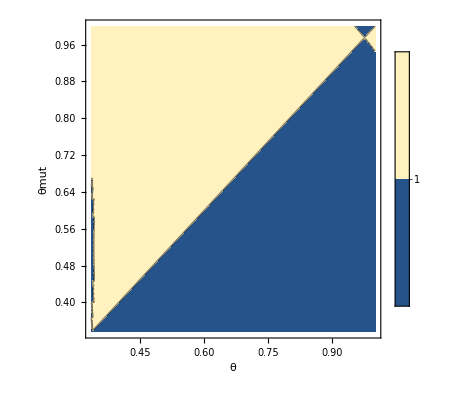

```mathematica
MyCplot = ContourPlot[Evaluate[W[θ,θmut, ESSparameters]] /.ESSparameters,{θ,0.336,1},{θmut,0.336,1},PlotRange->All, Contours->{1} ,FrameLabel->{θ, θmut} , PlotLegends->Automatic, PlotPoints->25]
```

```mathematica
SingleInfGradient[θESS_]:= D[WSupinf[θ,θmut],θmut]//. {θ-> θESS, θmut -> θESS};
```

```mathematica
d2Wdθmut2[θESS_]:= D[D[WSupinf[θ,θmut],θmut], θmut]//. {θ-> θESS, θmut -> θESS};
d2Wdθ2[θESS_]:=D[D[WSupinf[θ,θmut],θ], θ]//. {θ-> θESS, θmut -> θESS};
```

## Host and Parasite Gradients

```mathematica
ParasiteGradientSupinf[σESS_,θESS_]:= SingleInfGradient[θESS]//. σ-> σESS
HostGradient[σESS_,θESS_] :=MarginalFitness[σESS]//. θ-> θESS
```

```mathematica
ParasiteGradient[σESS_,θESS_]:= SingleInfGradient[θESS]//. σ-> σESS
HostGradient[σESS_, θESS_]:=D[NGTFitnessFunction[σ,σmut], σmut] //. σ-> σESS //. σmut -> σESS //. θ-> θESS
```

```mathematica
HostSecondDESS[σESS_, θESS_]:=d2Wdσmut2[σESS]/. θ-> θESS;
HostSecondDCSS[σESS_, θESS_]:= d2Wdσ2[σESS] /. θ-> θESS;
```

```mathematica
ParasiteSecondDESSSupinf[σESS_, θESS_]:= d2Wdθmut2[θESS]/. σ-> σESS;
ParasiteSecondDCSSSupinf[σESS_, θESS_]:= d2Wdθ2[θESS]/. σ-> σESS;
```

## Co-Singular strategies & Optimization principles

### Dispersal (conditions the force of infection)

#### Singular strategies VS parameter (superinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
PhaseplanSupinf = {}
ParamViruSupinf  = {}
ParamResiSupinf  = {}
RcsvListSupinf = {}
Do[
Print[dd];
(*Step I : Evaluate the expressions*)
NumCoESSParasite= ParasiteGradientSupinf[σESS, θESS]//. ESSparameters //. d-> dd; (*Evaluate fitness for current param value *)
NumCoESSHost= HostGradient[σESS, θESS]//. ESSparameters //. d-> dd;

(*Step II : Find couples of values where both expression vanishes*)
ListCandidates = {};
Do[
Do[
MyRoot = FindRoot[{NumCoESSParasite==0 , NumCoESSHost==0},{{σESS, hh},{ θESS,ii}}];
AppendTo[ListCandidates, MyRoot];
,{hh,1/10,0.99,1/10}];
,{ii,1/10,0.99,1/10}];


(*Step III : Delete duplicates*)
UniqueCandidates = {};
Do[
If[(ListCandidates[[i]][[1]][[2]] != ListCandidates[[i+1]][[1]][[2]]||ListCandidates[[i]][[2]][[2]] != ListCandidates[[i+1]][[2]][[2]] ),AppendTo[UniqueCandidates,ListCandidates[[i]]]] ; 

,{i,1,Length[ListCandidates]-1}];
AppendTo[UniqueCandidates,ListCandidates[[Length[ListCandidates]]]]; (* Add the last element, quick & dirty *)

(*Step IV : Keep only viable candidates*)
ViableCandidates = {};

Do[
Testedσ = σESS /. UniqueCandidates[[i]][[1]];
Testedθ=θESS /. UniqueCandidates[[i]][[2]];

(* Step IV.5 : Avoid σ / θ out of their validity domain*)

PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. d-> dd];
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. d-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //. d-> dd];


If[(1>=PS>=0 && 1>= PI >0 && X>0),AppendTo[ViableCandidates,{Testedσ, Testedθ}]] ; 
,{i,1,Length[UniqueCandidates]}];
(*Step V : Check for ESS  & Convergence stability*)
EssStableCouples ={};

Do[

Testedσ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedθ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;

If[( HostD2mut<0 &&ParasiteD2mut < 0),AppendTo[EssStableCouples ,{dd,Testedσ, Testedθ}]] ; 
,{i,1,Length[ViableCandidates]}];
(* Step ? : Check for Repellors*)
Do[
Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];


If[(Re[EG1]>=0 || Re[EG2]>=0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanSupinf , {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruSupinf ,{dd,EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiSupinf ,{dd,EssStableCouples[[i]][[2]], "REP"}]]; ];
,{i,1,Length[EssStableCouples]}];
(*Check for CSS*)
Do[

Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];

If[(Re[EG1]<0 && Re[EG2]<0),
Upperlimit = Evaluate[1+(γ0 EssStableCouples[[i]][[2]])/β0]//.ESSparameters;

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit  ),AppendTo[PhaseplanSupinf , {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]],dd}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[RcsvListSupinf , {dd,EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]]}]];
If[(dd > 0.51 &&0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[ParamViruSupinf ,{dd,EssStableCouples[[i]][[3]], dd}]];
If[( dd > 0.51 &&0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[ParamResiSupinf ,{dd,EssStableCouples[[i]][[2]], dd}]];
];
,{i,1,Length[EssStableCouples]}];

(* Step VI : Check for branching points just in case*)
Do[

Testedθ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedσ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d->dd;
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1 = EgVals[[1]];
EG2 = EgVals[[2]];
If[( HostD2mut>=0 &&ParasiteD2mut >= 0 && Re[EG1]<0 && Re[EG2]< 0),
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[PhaseplanSupinf , {Testedθ,Testedσ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamViruSupinf ,{dd,Testedθ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamResiSupinf ,{dd,Testedσ, "BP"}]];] ; 
,{i,1,Length[ViableCandidates]}];



,{dd,0.01,10,0.1}];
```

{}

{}

{}

«1 more identical outputs»

0.01

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-4.09811×10^14,-4.09811×10^13}. Try perturbing the initial point(s).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {2.53922×10^29,1.58255×10^28}. Try perturbing the initial point(s).

0.11

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-8.99306×10^27,-1.97935×10^27}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

0.21

GreaterEqual::nord: Invalid comparison with 2.54091-0.0517909 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.58729+0.052115 ⅈ attempted.

Greater::nord: Invalid comparison with 18.497+0.354915 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

0.31

0.41

0.51

0.61

0.71

0.81

0.91

1.01

1.11

1.21

1.31

1.41

1.51

1.61

1.71

1.81

1.91

2.01

2.11

2.21

2.31

2.41

2.51

2.61

2.71

2.81

2.91

3.01

3.11

3.21

3.31

3.41

3.51

3.61

3.71

3.81

3.91

4.01

4.11

4.21

4.31

4.41

4.51

4.61

4.71

4.81

4.91

5.01

5.11

5.21

5.31

5.41

5.51

5.61

5.71

5.81

5.91

6.01

6.11

6.21

6.31

6.41

6.51

6.61

6.71

6.81

6.91

7.01

7.11

7.21

7.31

7.41

7.51

7.61

7.71

7.81

7.91

8.01

8.11

8.21

8.31

8.41

8.51

8.61

8.71

8.81

8.91

9.01

9.11

9.21

9.31

9.41

9.51

9.61

9.71

9.81

9.91

```mathematica
(*dataps1=SplitBy[SortBy[PhaseplanSupinf ,Last],Last];

PS1 =Module[{categories=(#[[1,-1]]&/@dataps1)},ListPlot[#[[All,1;;2]]&/@dataps1,Frame->True,Axes->False,PlotStyle->{ ( ColorData[97][color[#]]&/@categories), PointSize[Medium]},FrameLabel->{Style["θESS", Bold, 14],Style["σESS", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, PlotRange->Full, Background->White]]
```

#### R0 optimisation (superinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
Sdfe = (b0-d0)/b0
```

(b0-d0)/b0

```mathematica
R0epi[σ_,θ_]:= d(1-ρ) Xeq[σ,θ] Sdfe/ (τ[σ, θ]+ α[σ,θ]+d0);
```

```mathematica
R0epi[0.5, 0.5]
```

-(d (b0-d0) (d-0.5 β0+0.5 γ0+μ) (1-ρ))/(b0 β1 (d0+(α0 (d-0.5 β0+0.5 γ0+μ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.5 β0+0.5 γ0+μ))/(d-β0+μ)))+((1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)))))

```mathematica
RcsvListSupinf
```

{{0.11,0.49596,0.952333},{0.11,0.49596,0.952333},{0.11,0.49596,0.952333},{0.21,0.447455,0.976329},{0.31,0.4397,0.989661},{0.31,0.4397,0.989661},{0.31,0.4397,0.989661},{0.41,0.439626,0.998118},{0.51,0.441903,1.00401},{0.61,0.445086,1.00839},{0.71,0.448666,1.01181},{0.81,0.452439,1.01457},{0.91,0.456311,1.01686},{1.01,0.460239,1.01882},{1.11,0.464201,1.02052},{1.21,0.468185,1.02202},{1.21,0.468185,1.02202},{1.31,0.472187,1.02337},{1.31,0.472187,1.02337},{1.41,0.476205,1.02459},{1.41,0.476205,1.02459},{1.51,0.480237,1.02571},{1.51,0.480237,1.02571},{1.51,0.480237,1.02571},{1.61,0.484284,1.02675},{1.61,0.484284,1.02675},{1.61,0.484284,1.02675},{1.71,0.488347,1.02771},{1.71,0.488347,1.02771},{1.81,0.492427,1.02863},{1.81,0.492427,1.02863},{1.91,0.496525,1.02949},{1.91,0.496525,1.02949},{2.01,0.500643,1.03031},{2.11,0.50478,1.0311},{2.21,0.508939,1.03186},{2.31,0.513121,1.03259},{2.41,0.517327,1.0333},{2.41,0.517327,1.0333},{2.51,0.521558,1.03399},{2.51,0.521558,1.03399},{2.61,0.525815,1.03467},{2.61,0.525815,1.03467},{2.71,0.530099,1.03533},{2.71,0.530099,1.03533},{2.81,0.534412,1.03598},{2.81,0.534412,1.03598},{2.91,0.538754,1.03663},{2.91,0.538754,1.03663},{3.01,0.543126,1.03726},{3.01,0.543126,1.03726},{3.11,0.547531,1.03789},{3.21,0.551968,1.03851},{3.31,0.556438,1.03912},{3.41,0.560944,1.03974},{3.51,0.565486,1.04035},{3.61,0.570065,1.04096},{3.61,0.570065,1.04096},{3.71,0.574683,1.04157},{3.71,0.574683,1.04157},{3.81,0.57934,1.04218},{3.81,0.57934,1.04218},{3.91,0.584039,1.04279},{3.91,0.584039,1.04279},{4.01,0.58878,1.0434},{4.01,0.58878,1.0434},{4.11,0.593565,1.04401},{4.11,0.593565,1.04401},{4.21,0.598395,1.04462},{4.21,0.598395,1.04462},{4.31,0.603272,1.04524},{4.31,0.603272,1.04524},{4.41,0.608197,1.04586},{4.41,0.608197,1.04586},{4.51,0.613172,1.04649},{4.51,0.613172,1.04649},{4.61,0.618198,1.04712},{4.61,0.618198,1.04712},{4.61,0.618198,1.04712},{4.71,0.623278,1.04775},{4.71,0.623278,1.04775},{4.71,0.623278,1.04775},{4.81,0.628414,1.04839},{4.81,0.628414,1.04839},{4.81,0.628414,1.04839},{4.91,0.633606,1.04904},{4.91,0.633606,1.04904},{4.91,0.633606,1.04904},{5.01,0.638858,1.04969},{5.01,0.638858,1.04969},{5.11,0.644172,1.05035},{5.11,0.644172,1.05035},{5.21,0.649549,1.05102},{5.21,0.649549,1.05102},{5.31,0.654993,1.0517},{5.31,0.654993,1.0517},{5.41,0.660505,1.05238},{5.41,0.660505,1.05238},{5.51,0.66609,1.05308},{5.51,0.66609,1.05308},{5.51,0.66609,1.05308},{5.61,0.671749,1.05378},{5.61,0.671749,1.05378},{5.61,0.671749,1.05378},{5.71,0.677486,1.0545},{5.71,0.677486,1.0545},{5.71,0.677486,1.0545},{5.81,0.683304,1.05522},{5.81,0.683304,1.05522},{5.81,0.683304,1.05522},{5.91,0.689207,1.05596},{5.91,0.689207,1.05596},{5.91,0.689207,1.05596},{6.01,0.695198,1.05671},{6.01,0.695198,1.05671},{6.11,0.701283,1.05747},{6.11,0.701283,1.05747},{6.21,0.707465,1.05824},{6.31,0.713749,1.05903},{6.41,0.72014,1.05984},{6.51,0.726645,1.06066},{6.61,0.733269,1.0615},{6.61,0.733269,1.0615},{6.71,0.74002,1.06235},{6.71,0.74002,1.06235},{6.81,0.746904,1.06323},{6.81,0.746904,1.06323},{6.81,0.746904,1.06323},{6.91,0.75393,1.06412},{6.91,0.75393,1.06412},{7.01,0.761107,1.06504},{7.01,0.761107,1.06504},{7.01,0.761107,1.06504},{7.11,0.768446,1.06599},{7.21,0.775956,1.06695},{7.31,0.783652,1.06795},{7.41,0.791546,1.06897},{7.51,0.799655,1.07002},{7.61,0.807998,1.07111},{7.61,0.807998,1.07111},{7.71,0.816594,1.07224},{7.91,0.834648,1.07461},{8.01,0.844167,1.07587}}

```mathematica
RcsvListSupinf[[1]]
```

{0.11,0.49596,0.952333}

```mathematica
(* 1st step : Get the parameter domain for which Rm >= 1*)
Do[
Upperlimit = Evaluate[1+(γ0 RcsvListSupinf[[i]][[2]])/β0]//.ESSparameters;

Maxim =NMaximize[{R0epi[RcsvListSupinf[[i]][[2]],θ]/. ESSparameters /. d->RcsvListSupinf[[i]][[1]] , 0<= θ<=Upperlimit},θ];
AppendTo[RcsvListSupinf[[i]],  θ/.Maxim[[2]]];
,{i,1,Length[RcsvListSupinf],1}];
Print[RcsvListSupinf];
```

{{0.11,0.49596,0.952333,0.899433},{0.11,0.49596,0.952333,0.899433},{0.11,0.49596,0.952333,0.899433},{0.21,0.447455,0.976329,0.896182},{0.31,0.4397,0.989661,0.897005},{0.31,0.4397,0.989661,0.897005},{0.31,0.4397,0.989661,0.897005},{0.41,0.439626,0.998118,0.898597},{0.51,0.441903,1.00401,0.900424},{0.61,0.445086,1.00839,0.902341},{0.71,0.448666,1.01181,0.904299},{0.81,0.452439,1.01457,0.906275},{0.91,0.456311,1.01686,0.908262},{1.01,0.460239,1.01882,0.910253},{1.11,0.464201,1.02052,0.912249},{1.21,0.468185,1.02202,0.914246},{1.21,0.468185,1.02202,0.914246},{1.31,0.472187,1.02337,0.916246},{1.31,0.472187,1.02337,0.916246},{1.41,0.476205,1.02459,0.918247},{1.41,0.476205,1.02459,0.918247},{1.51,0.480237,1.02571,0.920249},{1.51,0.480237,1.02571,0.920249},{1.51,0.480237,1.02571,0.920249},{1.61,0.484284,1.02675,0.922253},{1.61,0.484284,1.02675,0.922253},{1.61,0.484284,1.02675,0.922253},{1.71,0.488347,1.02771,0.924259},{1.71,0.488347,1.02771,0.924259},{1.81,0.492427,1.02863,0.926266},{1.81,0.492427,1.02863,0.926266},{1.91,0.496525,1.02949,0.928275},{1.91,0.496525,1.02949,0.928275},{2.01,0.500643,1.03031,0.930286},{2.11,0.50478,1.0311,0.932299},{2.21,0.508939,1.03186,0.934314},{2.31,0.513121,1.03259,0.936331},{2.41,0.517327,1.0333,0.938351},{2.41,0.517327,1.0333,0.938351},{2.51,0.521558,1.03399,0.940373},{2.51,0.521558,1.03399,0.940373},{2.61,0.525815,1.03467,0.942398},{2.61,0.525815,1.03467,0.942398},{2.71,0.530099,1.03533,0.944426},{2.71,0.530099,1.03533,0.944426},{2.81,0.534412,1.03598,0.946456},{2.81,0.534412,1.03598,0.946456},{2.91,0.538754,1.03663,0.948489},{2.91,0.538754,1.03663,0.948489},{3.01,0.543126,1.03726,0.950526},{3.01,0.543126,1.03726,0.950526},{3.11,0.547531,1.03789,0.952565},{3.21,0.551968,1.03851,0.954608},{3.31,0.556438,1.03912,0.956655},{3.41,0.560944,1.03974,0.958704},{3.51,0.565486,1.04035,0.960758},{3.61,0.570065,1.04096,0.962815},{3.61,0.570065,1.04096,0.962815},{3.71,0.574683,1.04157,0.964876},{3.71,0.574683,1.04157,0.964876},{3.81,0.57934,1.04218,0.966941},{3.81,0.57934,1.04218,0.966941},{3.91,0.584039,1.04279,0.96901},{3.91,0.584039,1.04279,0.96901},{4.01,0.58878,1.0434,0.971083},{4.01,0.58878,1.0434,0.971083},{4.11,0.593565,1.04401,0.973161},{4.11,0.593565,1.04401,0.973161},{4.21,0.598395,1.04462,0.975243},{4.21,0.598395,1.04462,0.975243},{4.31,0.603272,1.04524,0.97733},{4.31,0.603272,1.04524,0.97733},{4.41,0.608197,1.04586,0.979421},{4.41,0.608197,1.04586,0.979421},{4.51,0.613172,1.04649,0.981518},{4.51,0.613172,1.04649,0.981518},{4.61,0.618198,1.04712,0.98362},{4.61,0.618198,1.04712,0.98362},{4.61,0.618198,1.04712,0.98362},{4.71,0.623278,1.04775,0.985727},{4.71,0.623278,1.04775,0.985727},{4.71,0.623278,1.04775,0.985727},{4.81,0.628414,1.04839,0.98784},{4.81,0.628414,1.04839,0.98784},{4.81,0.628414,1.04839,0.98784},{4.91,0.633606,1.04904,0.989958},{4.91,0.633606,1.04904,0.989958},{4.91,0.633606,1.04904,0.989958},{5.01,0.638858,1.04969,0.992083},{5.01,0.638858,1.04969,0.992083},{5.11,0.644172,1.05035,0.994213},{5.11,0.644172,1.05035,0.994213},{5.21,0.649549,1.05102,0.99635},{5.21,0.649549,1.05102,0.99635},{5.31,0.654993,1.0517,0.998494},{5.31,0.654993,1.0517,0.998494},{5.41,0.660505,1.05238,1.00064},{5.41,0.660505,1.05238,1.00064},{5.51,0.66609,1.05308,1.0028},{5.51,0.66609,1.05308,1.0028},{5.51,0.66609,1.05308,1.0028},{5.61,0.671749,1.05378,1.00497},{5.61,0.671749,1.05378,1.00497},{5.61,0.671749,1.05378,1.00497},{5.71,0.677486,1.0545,1.00714},{5.71,0.677486,1.0545,1.00714},{5.71,0.677486,1.0545,1.00714},{5.81,0.683304,1.05522,1.00932},{5.81,0.683304,1.05522,1.00932},{5.81,0.683304,1.05522,1.00932},{5.91,0.689207,1.05596,1.01151},{5.91,0.689207,1.05596,1.01151},{5.91,0.689207,1.05596,1.01151},{6.01,0.695198,1.05671,1.01371},{6.01,0.695198,1.05671,1.01371},{6.11,0.701283,1.05747,1.01592},{6.11,0.701283,1.05747,1.01592},{6.21,0.707465,1.05824,1.01813},{6.31,0.713749,1.05903,1.02036},{6.41,0.72014,1.05984,1.0226},{6.51,0.726645,1.06066,1.02485},{6.61,0.733269,1.0615,1.02711},{6.61,0.733269,1.0615,1.02711},{6.71,0.74002,1.06235,1.02938},{6.71,0.74002,1.06235,1.02938},{6.81,0.746904,1.06323,1.03167},{6.81,0.746904,1.06323,1.03167},{6.81,0.746904,1.06323,1.03167},{6.91,0.75393,1.06412,1.03397},{6.91,0.75393,1.06412,1.03397},{7.01,0.761107,1.06504,1.03629},{7.01,0.761107,1.06504,1.03629},{7.01,0.761107,1.06504,1.03629},{7.11,0.768446,1.06599,1.03862},{7.21,0.775956,1.06695,1.04097},{7.31,0.783652,1.06795,1.04334},{7.41,0.791546,1.06897,1.04573},{7.51,0.799655,1.07002,1.04814},{7.61,0.807998,1.07111,1.05058},{7.61,0.807998,1.07111,1.05058},{7.71,0.816594,1.07224,1.05303},{7.91,0.834648,1.07461,1.05804},{8.01,0.844167,1.07587,1.06059}}

```mathematica
Export["C:\\Users\\Julien\\Desktop\\CSV coevolution Mathematica pour figures sur R ce titre est trop long\\Dispersal\\DispersalSupinfFinal.csv",RcsvListSupinf,"csv"]
```

C:\Users\Julien\Desktop\CSV coevolution Mathematica pour figures sur R ce titre est trop long\Dispersal\DispersalSupinfFinal.csv

### Recovery (conditions the infectious period)

#### Singular strategies VS parameter (superinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, d->0.5,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,d→0.5,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
PhaseplanSupinf = {}
ParamViruSupinf  = {}
ParamResiSupinf  = {}
RcsvListSupinf = {}
Do[
Print[dd];
(*Step I : Evaluate the expressions*)
NumCoESSParasite= ParasiteGradientSupinf[σESS, θESS]//. ESSparameters //. τ0-> dd; (*Evaluate fitness for current param value *)
NumCoESSHost= HostGradient[σESS, θESS]//. ESSparameters //. τ0-> dd;

(*Step II : Find couples of values where both expression vanishes*)
ListCandidates = {};
Do[
Do[
MyRoot = FindRoot[{NumCoESSParasite==0 , NumCoESSHost==0},{{σESS, hh},{ θESS,ii}}];
AppendTo[ListCandidates, MyRoot];
,{hh,1/10,0.99,1/10}];
,{ii,1/10,0.99,1/10}];


(*Step III : Delete duplicates*)
UniqueCandidates = {};
Do[
If[(ListCandidates[[i]][[1]][[2]] != ListCandidates[[i+1]][[1]][[2]]||ListCandidates[[i]][[2]][[2]] != ListCandidates[[i+1]][[2]][[2]] ),AppendTo[UniqueCandidates,ListCandidates[[i]]]] ; 

,{i,1,Length[ListCandidates]-1}];
AppendTo[UniqueCandidates,ListCandidates[[Length[ListCandidates]]]]; (* Add the last element, quick & dirty *)

(*Step IV : Keep only viable candidates*)
ViableCandidates = {};

Do[
Testedσ = σESS /. UniqueCandidates[[i]][[1]];
Testedθ=θESS /. UniqueCandidates[[i]][[2]];

(* Step IV.5 : Avoid σ / θ out of their validity domain*)

PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. τ0-> dd];
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. τ0-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //.τ0-> dd];


If[(1>=PS>=0 && 1>= PI >0 && X>0),AppendTo[ViableCandidates,{Testedσ, Testedθ}]] ; 
,{i,1,Length[UniqueCandidates]}];
(*Step V : Check for ESS  & Convergence stability*)
EssStableCouples ={};

Do[

Testedσ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedθ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;

If[( HostD2mut<0 &&ParasiteD2mut < 0),AppendTo[EssStableCouples ,{dd,Testedσ, Testedθ}]] ; 
,{i,1,Length[ViableCandidates]}];
(* Step ? : Check for Repellors*)
Do[
Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];


If[(Re[EG1]>=0 || Re[EG2]>=0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanSupinf , {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruSupinf ,{dd,EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiSupinf ,{dd,EssStableCouples[[i]][[2]], "REP"}]]; ];
,{i,1,Length[EssStableCouples]}];
(*Check for CSS*)
Do[

Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];

If[(Re[EG1]<0 && Re[EG2]<0),
Upperlimit = Evaluate[1+(γ0 EssStableCouples[[i]][[2]])/β0]//.ESSparameters;

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[PhaseplanSupinf , {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]],dd}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[RcsvListSupinf , {dd,EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]]}]];
If[(dd > 1.01 &&0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[ParamViruSupinf ,{dd,EssStableCouples[[i]][[3]], dd}]];
If[(dd > 1.01 &&0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[ParamResiSupinf ,{dd,EssStableCouples[[i]][[2]], dd}]];
];
,{i,1,Length[EssStableCouples]}];

(* Step VI : Check for branching points just in case*)
Do[

Testedθ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedσ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. τ0->dd;
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. τ0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1 = EgVals[[1]];
EG2 = EgVals[[2]];
If[( HostD2mut>=0 &&ParasiteD2mut >= 0 && Re[EG1]<0 && Re[EG2]< 0),
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[PhaseplanSupinf , {Testedθ,Testedσ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamViruSupinf ,{dd,Testedθ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamResiSupinf ,{dd,Testedσ, "BP"}]];] ; 
,{i,1,Length[ViableCandidates]}];



,{dd,0.01,7,0.1}];
```

{}

{}

{}

«1 more identical outputs»

0.01

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-2.07285×10^16,-1.92628×10^28}. Try perturbing the initial point(s).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {8.14035×10^15,-4.7669×10^27}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {2.23099×10^16,-2.56865×10^28}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

0.11

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.21

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.31

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with -0.0275556-2.71051×10^-20 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 1.23234+1.73472×10^-18 ⅈ attempted.

Greater::nord: Invalid comparison with -2.86799×10^31-1.47181×10^29 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

0.41

0.51

0.61

0.71

0.81

0.91

1.01

1.11

1.21

1.31

1.41

1.51

1.61

1.71

1.81

1.91

2.01

2.11

2.21

2.31

2.41

2.51

2.61

2.71

2.81

2.91

3.01

3.11

3.21

3.31

3.41

3.51

3.61

3.71

3.81

3.91

4.01

4.11

4.21

4.31

4.41

4.51

4.61

4.71

4.81

4.91

5.01

5.11

5.21

5.31

5.41

5.51

5.61

5.71

5.81

5.91

6.01

6.11

6.21

6.31

6.41

6.51

6.61

6.71

6.81

6.91

```mathematica
(*dataps1=SplitBy[SortBy[PhaseplanSupinf ,Last],Last];

PS1 =Module[{categories=(#[[1,-1]]&/@dataps1)},ListPlot[#[[All,1;;2]]&/@dataps1,Frame->True,Axes->False,PlotStyle->{ ( ColorData[97][color[#]]&/@categories), PointSize[Medium]},FrameLabel->{Style["θESS", Bold, 14],Style["σESS", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, PlotRange->Full, Background->White]]
```

#### R0 optimisation (superinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d0->0.05, d->0.5,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d0→0.05,d→0.5,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
Sdfe = (b0-d0)/b0
```

(b0-d0)/b0

```mathematica
R0epi[σ_,θ_]:= d(1-ρ) Xeq[σ,θ] Sdfe/ (τ[σ, θ]+ α[σ,θ]+d0);
```

```mathematica
R0epi[0.5, 0.5]
```

-(d (b0-d0) (d-0.5 β0+0.5 γ0+μ) (1-ρ))/(b0 β1 (d0+(α0 (d-0.5 β0+0.5 γ0+μ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.5 β0+0.5 γ0+μ))/(d-β0+μ)))+((1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)))))

```mathematica
RcsvListSupinf
```

```mathematica
RcsvListSupinf[[1]]
```

{0.11,0.49596,0.952333}

```mathematica
(* 1st step : Get the parameter domain for which Rm >= 1*)
Do[
Upperlimit = Evaluate[1+(γ0 RcsvListSupinf[[i]][[2]])/β0]//.ESSparameters;

Maxim =NMaximize[{R0epi[RcsvListSupinf[[i]][[2]],θ]/. ESSparameters /. τ0->RcsvListSupinf[[i]][[1]] , 0<= θ<=Upperlimit},θ];
AppendTo[RcsvListSupinf[[i]],  θ/.Maxim[[2]]];
,{i,1,Length[RcsvListSupinf],1}];
Print[RcsvListSupinf];
```

{{0.01,0.351517,0.964524,0.505066},{0.11,0.36132,0.968802,0.636132},{0.21,0.370971,0.973004,0.705112},{0.21,0.370971,0.973004,0.705112},{0.31,0.380466,0.977128,0.751683},{0.31,0.380466,0.977128,0.751683},{0.41,0.389804,0.981175,0.786571},{0.41,0.389804,0.981175,0.786571},{0.41,0.389804,0.981175,0.786571},{0.51,0.398984,0.985146,0.814297},{0.51,0.398984,0.985146,0.814297},{0.51,0.398984,0.985146,0.814297},{0.61,0.408002,0.98904,0.837197},{0.61,0.408002,0.98904,0.837197},{0.61,0.408002,0.98904,0.837197},{0.71,0.416859,0.992857,0.856635},{0.71,0.416859,0.992857,0.856635},{0.71,0.416859,0.992857,0.856635},{0.81,0.425553,0.996599,0.873472},{0.81,0.425553,0.996599,0.873472},{0.81,0.425553,0.996599,0.873472},{0.91,0.434084,1.00027,0.888288},{1.01,0.442452,1.00386,0.901493},{1.11,0.450657,1.00737,0.913383},{1.21,0.4587,1.01082,0.924182},{1.31,0.466582,1.01419,0.934062},{1.31,0.466582,1.01419,0.934062},{1.41,0.474304,1.01749,0.943157},{1.41,0.474304,1.01749,0.943157},{1.51,0.481867,1.02072,0.951574},{1.51,0.481867,1.02072,0.951574},{1.61,0.489274,1.02389,0.959402},{1.61,0.489274,1.02389,0.959402},{1.71,0.496526,1.02698,0.966712},{1.71,0.496526,1.02698,0.966712},{1.81,0.503626,1.03001,0.973563},{1.81,0.503626,1.03001,0.973563},{1.91,0.510575,1.03297,0.980005},{1.91,0.510575,1.03297,0.980005},{1.91,0.510575,1.03297,0.980005},{2.01,0.517376,1.03587,0.98608},{2.11,0.524032,1.03871,0.991826},{2.21,0.530545,1.04149,0.997272},{2.31,0.536918,1.0442,1.00245},{2.31,0.536918,1.0442,1.00245},{2.41,0.543155,1.04686,1.00737},{2.41,0.543155,1.04686,1.00737},{2.41,0.543155,1.04686,1.00737},{2.41,0.543155,1.04686,1.00737},{2.51,0.549257,1.04946,1.01207},{2.51,0.549257,1.04946,1.01207},{2.51,0.549257,1.04946,1.01207},{2.51,0.549257,1.04946,1.01207},{2.51,0.549257,1.04946,1.01207},{2.51,0.549257,1.04946,1.01207},{2.61,0.555228,1.05201,1.01656},{2.61,0.555228,1.05201,1.01656},{2.61,0.555228,1.05201,1.01656},{2.61,0.555228,1.05201,1.01656},{2.61,0.555228,1.05201,1.01656},{2.61,0.555228,1.05201,1.01656},{2.61,0.555228,1.05201,1.01656},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085},{2.71,0.56107,1.0545,1.02085}}

```mathematica
Export["C:\\Users\\Julien\\Desktop\\CSV coevolution Mathematica pour figures sur R ce titre est trop long\\Recovery\\RecoverySupinfFinal.csv",RcsvListSupinf,"csv"]
```

C:\Users\Julien\Desktop\CSV coevolution Mathematica pour figures sur R ce titre est trop long\Recovery\RecoverySupinfFinal.csv

### Background mortality (conditions the infectious period)

#### Singular strategies VS parameter (superinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d->0.5, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d→0.5,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
PhaseplanSupinf = {}
ParamViruSupinf  = {}
ParamResiSupinf  = {}
RcsvListSupinf = {}
Do[
Print[dd];
(*Step I : Evaluate the expressions*)
NumCoESSParasite= ParasiteGradientSupinf[σESS, θESS]//. ESSparameters //. d0-> dd; (*Evaluate fitness for current param value *)
NumCoESSHost= HostGradient[σESS, θESS]//. ESSparameters //. d0-> dd;

(*Step II : Find couples of values where both expression vanishes*)
ListCandidates = {};
Do[
Do[
MyRoot = FindRoot[{NumCoESSParasite==0 , NumCoESSHost==0},{{σESS, hh},{ θESS,ii}}];
AppendTo[ListCandidates, MyRoot];
,{hh,1/10,0.99,1/10}];
,{ii,1/10,0.99,1/10}];


(*Step III : Delete duplicates*)
UniqueCandidates = {};
Do[
If[(ListCandidates[[i]][[1]][[2]] != ListCandidates[[i+1]][[1]][[2]]||ListCandidates[[i]][[2]][[2]] != ListCandidates[[i+1]][[2]][[2]] ),AppendTo[UniqueCandidates,ListCandidates[[i]]]] ; 

,{i,1,Length[ListCandidates]-1}];
AppendTo[UniqueCandidates,ListCandidates[[Length[ListCandidates]]]]; (* Add the last element, quick & dirty *)

(*Step IV : Keep only viable candidates*)
ViableCandidates = {};

Do[
Testedσ = σESS /. UniqueCandidates[[i]][[1]];
Testedθ=θESS /. UniqueCandidates[[i]][[2]];

(* Step IV.5 : Avoid σ / θ out of their validity domain*)

PS = Evaluate[pS[Testedσ, Testedθ]//.ESSparameters//. d0-> dd];
PI = Evaluate[pI[Testedσ, Testedθ]//.ESSparameters //. d0-> dd];
X= Evaluate[Xeq[Testedσ, Testedθ]//.ESSparameters //. d0-> dd];


If[(1>=PS>=0 && 1>= PI >0 && X>0),AppendTo[ViableCandidates,{Testedσ, Testedθ}]] ; 
,{i,1,Length[UniqueCandidates]}];
(*Step V : Check for ESS  & Convergence stability*)
EssStableCouples ={};

Do[

Testedσ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedθ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;

If[( HostD2mut<0 &&ParasiteD2mut < 0),AppendTo[EssStableCouples ,{dd,Testedσ, Testedθ}]] ; 
,{i,1,Length[ViableCandidates]}];
(* Step ? : Check for Repellors*)
Do[
Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];


If[(Re[EG1]>=0 || Re[EG2]>=0),

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[PhaseplanSupinf , {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamViruSupinf ,{dd,EssStableCouples[[i]][[3]], "REP"}]];
If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=1 ),AppendTo[ParamResiSupinf ,{dd,EssStableCouples[[i]][[2]], "REP"}]]; ];
,{i,1,Length[EssStableCouples]}];
(*Check for CSS*)
Do[

Testedσ =  EssStableCouples[[i]][[2]]; (* Get the values*)
Testedθ=EssStableCouples[[i]][[3]];
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1= EgVals[[1]];
EG2 = EgVals[[2]];

If[(Re[EG1]<0 && Re[EG2]<0),
Upperlimit = Evaluate[1+(γ0 EssStableCouples[[i]][[2]])/β0]//.ESSparameters;

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit),AppendTo[PhaseplanSupinf , {EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]],dd}]];

If[(0<EssStableCouples[[i]][[2]]<=1 && 0<EssStableCouples[[i]][[3]]<=Upperlimit ),AppendTo[RcsvListSupinf , {dd,EssStableCouples[[i]][[2]],EssStableCouples[[i]][[3]]}]];

];
,{i,1,Length[EssStableCouples]}];

(* Step VI : Check for branching points just in case*)
Do[

Testedθ =  ViableCandidates[[i]][[1]]; (* Get the values*)

Testedσ= ViableCandidates[[i]][[2]];

HostD2mut =HostSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;

ParasiteD2mut = ParasiteSecondDESS[Testedσ,Testedθ ]//.ESSparameters //. d0->dd;
dHostdHost= D[HostGradient[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dHostdParasite= D[HostGradient[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedParasite= D[ParasiteGradientSupinf[σESS, θESS], θESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;
dParasitedHost= D[ParasiteGradientSupinf[σESS, θESS], σESS]//. σESS -> Testedσ//. θESS-> Testedθ  //. ESSparameters//. d0->dd;

JacCoevo = ({{dParasitedParasite, dParasitedHost}, {dHostdParasite, dHostdHost}});
EgVals = Eigenvalues[JacCoevo];
EG1 = EgVals[[1]];
EG2 = EgVals[[2]];
If[( HostD2mut>=0 &&ParasiteD2mut >= 0 && Re[EG1]<0 && Re[EG2]< 0),
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[PhaseplanSupinf , {Testedθ,Testedσ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamViruSupinf ,{dd,Testedθ, "BP"}]];
If[(0<Testedσ<=1 && 0<Testedθ<=1 ),AppendTo[ParamResiSupinf ,{dd,Testedσ, "BP"}]];] ; 
,{i,1,Length[ViableCandidates]}];



,{dd,0.01,0.7,0.02}];
```

{}

{}

{}

«1 more identical outputs»

0.01

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-7.68507×10^15,-7.93028×10^26}. Try perturbing the initial point(s).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-2.36519×10^28,-4.85029×10^27}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {σESS,θESS} = {-6.30744×10^28,-1.29333×10^28}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

0.03

GreaterEqual::nord: Invalid comparison with -3.50674+6.18093×10^-16 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with 4.58248-0.0715348 ⅈ attempted.

Greater::nord: Invalid comparison with -5.99664-1.07907×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

0.05

0.07

0.09

0.11

0.13

0.15

0.17

0.19

0.21

0.23

0.25

0.27

0.29

0.31

0.33

0.35

0.37

0.39

0.41

0.43

0.45

0.47

0.49

0.51

0.53

0.55

0.57

0.59

0.61

0.63

0.65

0.67

0.69

```mathematica
(*dataps1=SplitBy[SortBy[PhaseplanSupinf ,Last],Last];

PS1 =Module[{categories=(#[[1,-1]]&/@dataps1)},ListPlot[#[[All,1;;2]]&/@dataps1,Frame->True,Axes->False,PlotStyle->{ ( ColorData[97][color[#]]&/@categories), PointSize[Medium]},FrameLabel->{Style["θESS", Bold, 14],Style["σESS", Bold, 14]},AspectRatio->1,LabelStyle->{FontSize->13,FontFamily->"Helvetica",Black},ImageSize->360, PlotRange->Full, Background->White]]
```

#### R0 optimisation (superinfections)

```mathematica
ESSparameters={b0->0.8,  μ->0.5,  β0->10, β1->0.04,  ρ ->0.9 , d->0.5, τ0->1,  ϵ->5, α0->1, γ0->1, ϵv->5, ϵr->1}
```

{b0→0.8,μ→0.5,β0→10,β1→0.04,ρ→0.9,d→0.5,τ0→1,ϵ→5,α0→1,γ0→1,ϵv→5,ϵr→1}

```mathematica
Sdfe = (b0-d0)/b0
```

(b0-d0)/b0

```mathematica
R0epi[σ_,θ_]:= d(1-ρ) Xeq[σ,θ] Sdfe/ (τ[σ, θ]+ α[σ,θ]+d0);
```

```mathematica
R0epi[0.5, 0.5]
```

-(d (b0-d0) (d-0.5 β0+0.5 γ0+μ) (1-ρ))/(b0 β1 (d0+(α0 (d-0.5 β0+0.5 γ0+μ))/((d-β0+μ) (ϵv-((-1+ϵv) (d-0.5 β0+0.5 γ0+μ))/(d-β0+μ)))+((1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)) τ0)/(ϵr-(-1+ϵr) (1-(d-0.5 β0+0.5 γ0+μ)/(d-β0+μ)))))

```mathematica
RcsvListSupinf
```

{{0.01,0.456896,1.00826},{0.03,0.449253,1.00588},{0.05,0.441622,1.0035},{0.07,0.434008,1.00113},{0.07,0.434008,1.00113},{0.09,0.426412,0.998758},{0.09,0.426412,0.998758},{0.09,0.426412,0.998758},{0.11,0.418839,0.996393},{0.11,0.418839,0.996393},{0.11,0.418839,0.996393},{0.13,0.411291,0.994035},{0.13,0.411291,0.994035},{0.15,0.40377,0.991684},{0.15,0.40377,0.991684},{0.15,0.40377,0.991684},{0.17,0.39628,0.989342},{0.17,0.39628,0.989342},{0.17,0.39628,0.989342},{0.17,0.39628,0.989342},{0.19,0.388824,0.987009},{0.19,0.388824,0.987009},{0.19,0.388824,0.987009},{0.19,0.388824,0.987009},{0.21,0.381405,0.984685},{0.21,0.381405,0.984685},{0.21,0.381405,0.984685},{0.21,0.381405,0.984685},{0.23,0.374025,0.982374},{0.23,0.374025,0.982374},{0.23,0.374025,0.982374},{0.23,0.374025,0.982374},{0.23,0.374025,0.982374},{0.25,0.366688,0.980074},{0.25,0.366688,0.980074},{0.25,0.366688,0.980074},{0.25,0.366688,0.980074},{0.27,0.359397,0.977787},{0.27,0.359397,0.977787},{0.27,0.359397,0.977787},{0.29,0.352154,0.975515},{0.29,0.352154,0.975515},{0.31,0.344962,0.973257},{0.31,0.344962,0.973257},{0.31,0.344962,0.973257},{0.31,0.344962,0.973257},{0.31,0.344962,0.973257},{0.31,0.344962,0.973257},{0.33,0.337824,0.971016},{0.33,0.337824,0.971016},{0.35,0.330743,0.968791},{0.35,0.330743,0.968791},{0.37,0.32372,0.966583},{0.37,0.32372,0.966583},{0.37,0.32372,0.966583},{0.37,0.32372,0.966583},{0.39,0.316759,0.964395},{0.39,0.316759,0.964395},{0.39,0.316759,0.964395},{0.39,0.316759,0.964395},{0.39,0.316759,0.964395},{0.41,0.309862,0.962225},{0.41,0.309862,0.962225},{0.41,0.309862,0.962225},{0.41,0.309862,0.962225},{0.41,0.309862,0.962225},{0.41,0.309862,0.962225},{0.41,0.309862,0.962225},{0.43,0.303031,0.960076},{0.43,0.303031,0.960076},{0.43,0.303031,0.960076},{0.43,0.303031,0.960076},{0.43,0.303031,0.960076},{0.43,0.303031,0.960076},{0.45,0.296268,0.957947},{0.45,0.296268,0.957947},{0.45,0.296268,0.957947},{0.45,0.296268,0.957947},{0.45,0.296268,0.957947},{0.47,0.289575,0.955839},{0.47,0.289575,0.955839},{0.47,0.289575,0.955839},{0.47,0.289575,0.955839},{0.47,0.289575,0.955839},{0.47,0.289575,0.955839},{0.49,0.282955,0.953754},{0.49,0.282955,0.953754},{0.49,0.282955,0.953754},{0.49,0.282955,0.953754},{0.49,0.282955,0.953754},{0.49,0.282955,0.953754},{0.51,0.276408,0.951691},{0.51,0.276408,0.951691},{0.51,0.276408,0.951691},{0.51,0.276408,0.951691},{0.53,0.269937,0.949651},{0.53,0.269937,0.949651},{0.53,0.269937,0.949651},{0.53,0.269937,0.949651},{0.53,0.269937,0.949651},{0.53,0.269937,0.949651},{0.55,0.263543,0.947635},{0.55,0.263543,0.947635},{0.55,0.263543,0.947635},{0.57,0.257227,0.945643},{0.57,0.257227,0.945643},{0.57,0.257227,0.945643},{0.57,0.257227,0.945643},{0.57,0.257227,0.945643},{0.57,0.257227,0.945643},{0.57,0.257227,0.945643},{0.59,0.250992,0.943676},{0.59,0.250992,0.943676},{0.59,0.250992,0.943676},{0.59,0.250992,0.943676},{0.59,0.250992,0.943676},{0.61,0.244837,0.941734},{0.61,0.244837,0.941734},{0.61,0.244837,0.941734},{0.61,0.244837,0.941734},{0.61,0.244837,0.941734},{0.61,0.244837,0.941734},{0.61,0.244837,0.941734},{0.63,0.238763,0.939817},{0.63,0.238763,0.939817},{0.63,0.238763,0.939817},{0.63,0.238763,0.939817},{0.63,0.238763,0.939817},{0.63,0.238763,0.939817},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.65,0.232773,0.937925},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059},{0.67,0.226866,0.936059}}

```mathematica
RcsvListSupinf[[1]]
```

{0.01,0.456896,1}

```mathematica
(* 1st step : Get the parameter domain for which Rm >= 1*)
Do[
Upperlimit = Evaluate[1+(γ0 RcsvListSupinf[[i]][[2]])/β0]//.ESSparameters;
Maxim =NMaximize[{R0epi[RcsvListSupinf[[i]][[2]],θ]/. ESSparameters /. d0->RcsvListSupinf[[i]][[1]] , 0<= θ<=Upperlimit},θ];
AppendTo[RcsvListSupinf[[i]],  θ/.Maxim[[2]]];
,{i,1,Length[RcsvListSupinf],1}];
Print[RcsvListSupinf];
```

{{0.01,0.456896,1.00826,0.896932},{0.03,0.449253,1.00588,0.898611},{0.05,0.441622,1.0035,0.900236},{0.07,0.434008,1.00113,0.90181},{0.07,0.434008,1.00113,0.90181},{0.09,0.426412,0.998758,0.903335},{0.09,0.426412,0.998758,0.903335},{0.09,0.426412,0.998758,0.903335},{0.11,0.418839,0.996393,0.904814},{0.11,0.418839,0.996393,0.904814},{0.11,0.418839,0.996393,0.904814},{0.13,0.411291,0.994035,0.906248},{0.13,0.411291,0.994035,0.906248},{0.15,0.40377,0.991684,0.907639},{0.15,0.40377,0.991684,0.907639},{0.15,0.40377,0.991684,0.907639},{0.17,0.39628,0.989342,0.90899},{0.17,0.39628,0.989342,0.90899},{0.17,0.39628,0.989342,0.90899},{0.17,0.39628,0.989342,0.90899},{0.19,0.388824,0.987009,0.910303},{0.19,0.388824,0.987009,0.910303},{0.19,0.388824,0.987009,0.910303},{0.19,0.388824,0.987009,0.910303},{0.21,0.381405,0.984685,0.911578},{0.21,0.381405,0.984685,0.911578},{0.21,0.381405,0.984685,0.911578},{0.21,0.381405,0.984685,0.911578},{0.23,0.374025,0.982374,0.912818},{0.23,0.374025,0.982374,0.912818},{0.23,0.374025,0.982374,0.912818},{0.23,0.374025,0.982374,0.912818},{0.23,0.374025,0.982374,0.912818},{0.25,0.366688,0.980074,0.914025},{0.25,0.366688,0.980074,0.914025},{0.25,0.366688,0.980074,0.914025},{0.25,0.366688,0.980074,0.914025},{0.27,0.359397,0.977787,0.915199},{0.27,0.359397,0.977787,0.915199},{0.27,0.359397,0.977787,0.915199},{0.29,0.352154,0.975515,0.916343},{0.29,0.352154,0.975515,0.916343},{0.31,0.344962,0.973257,0.917458},{0.31,0.344962,0.973257,0.917458},{0.31,0.344962,0.973257,0.917458},{0.31,0.344962,0.973257,0.917458},{0.31,0.344962,0.973257,0.917458},{0.31,0.344962,0.973257,0.917458},{0.33,0.337824,0.971016,0.918545},{0.33,0.337824,0.971016,0.918545},{0.35,0.330743,0.968791,0.919605},{0.35,0.330743,0.968791,0.919605},{0.37,0.32372,0.966583,0.92064},{0.37,0.32372,0.966583,0.92064},{0.37,0.32372,0.966583,0.92064},{0.37,0.32372,0.966583,0.92064},{0.39,0.316759,0.964395,0.921652},{0.39,0.316759,0.964395,0.921652},{0.39,0.316759,0.964395,0.921652},{0.39,0.316759,0.964395,0.921652},{0.39,0.316759,0.964395,0.921652},{0.41,0.309862,0.962225,0.92264},{0.41,0.309862,0.962225,0.92264},{0.41,0.309862,0.962225,0.92264},{0.41,0.309862,0.962225,0.92264},{0.41,0.309862,0.962225,0.92264},{0.41,0.309862,0.962225,0.92264},{0.41,0.309862,0.962225,0.92264},{0.43,0.303031,0.960076,0.923606},{0.43,0.303031,0.960076,0.923606},{0.43,0.303031,0.960076,0.923606},{0.43,0.303031,0.960076,0.923606},{0.43,0.303031,0.960076,0.923606},{0.43,0.303031,0.960076,0.923606},{0.45,0.296268,0.957947,0.924552},{0.45,0.296268,0.957947,0.924552},{0.45,0.296268,0.957947,0.924552},{0.45,0.296268,0.957947,0.924552},{0.45,0.296268,0.957947,0.924552},{0.47,0.289575,0.955839,0.925478},{0.47,0.289575,0.955839,0.925478},{0.47,0.289575,0.955839,0.925478},{0.47,0.289575,0.955839,0.925478},{0.47,0.289575,0.955839,0.925478},{0.47,0.289575,0.955839,0.925478},{0.49,0.282955,0.953754,0.926385},{0.49,0.282955,0.953754,0.926385},{0.49,0.282955,0.953754,0.926385},{0.49,0.282955,0.953754,0.926385},{0.49,0.282955,0.953754,0.926385},{0.49,0.282955,0.953754,0.926385},{0.51,0.276408,0.951691,0.927274},{0.51,0.276408,0.951691,0.927274},{0.51,0.276408,0.951691,0.927274},{0.51,0.276408,0.951691,0.927274},{0.53,0.269937,0.949651,0.928147},{0.53,0.269937,0.949651,0.928147},{0.53,0.269937,0.949651,0.928147},{0.53,0.269937,0.949651,0.928147},{0.53,0.269937,0.949651,0.928147},{0.53,0.269937,0.949651,0.928147},{0.55,0.263543,0.947635,0.929003},{0.55,0.263543,0.947635,0.929003},{0.55,0.263543,0.947635,0.929003},{0.57,0.257227,0.945643,0.929844},{0.57,0.257227,0.945643,0.929844},{0.57,0.257227,0.945643,0.929844},{0.57,0.257227,0.945643,0.929844},{0.57,0.257227,0.945643,0.929844},{0.57,0.257227,0.945643,0.929844},{0.57,0.257227,0.945643,0.929844},{0.59,0.250992,0.943676,0.93067},{0.59,0.250992,0.943676,0.93067},{0.59,0.250992,0.943676,0.93067},{0.59,0.250992,0.943676,0.93067},{0.59,0.250992,0.943676,0.93067},{0.61,0.244837,0.941734,0.931482},{0.61,0.244837,0.941734,0.931482},{0.61,0.244837,0.941734,0.931482},{0.61,0.244837,0.941734,0.931482},{0.61,0.244837,0.941734,0.931482},{0.61,0.244837,0.941734,0.931482},{0.61,0.244837,0.941734,0.931482},{0.63,0.238763,0.939817,0.932281},{0.63,0.238763,0.939817,0.932281},{0.63,0.238763,0.939817,0.932281},{0.63,0.238763,0.939817,0.932281},{0.63,0.238763,0.939817,0.932281},{0.63,0.238763,0.939817,0.932281},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.65,0.232773,0.937925,0.933067},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841},{0.67,0.226866,0.936059,0.933841}}

```mathematica
Export["C:\\Users\\Julien\\Desktop\\CSV coevolution Mathematica pour figures sur R ce titre est trop long\\Background Mortality\\BGmortalitySupinfFinal.csv",RcsvListSupinf,"csv"]
```

C:\Users\Julien\Desktop\CSV coevolution Mathematica pour figures sur R ce titre est trop long\Background Mortality\BGmortalitySupinfFinal.csv